```mathematica
po
```

# Combined Analysis Ω_DM and Direct Detection limits from lux

```mathematica
SetDirectory["/home/vanniagm/Dropbox/nu_portal/MATH_NUMODEL/"];
```

List of model parameters

#### Relative Abundance

#### Ω=0.1198+-0.0026

```mathematica
Ωexp = 0.1198; Ωerr = 0.0026; 
vev = 246; 
time1 = SessionTime[];
```

#### Abundance Plot

Degenerate masses case, mphi~mpsi for mpsi > 62  Both cases , deg. and non - deg are included for mpsi < 62

```mathematica
omf2G=Join[Import["mpsi_1_200.dat"],Import["mpsims.840.dat"],Import["mpsims.1550.dat"],Import["mpsims.1000.dat"],Import["mpsims.850.dat"],Import["mpsims.1260.dat"],Import["mpsims.810.dat"],Import["mpsims.920.dat"],Import["mpsims.930.dat"],Import["mpsims.1300.dat"],Import["mpsims.925.dat"],Import["mpsims.825.dat"],Import["mpsims.1270.dat"]];Length[omf2G]
```

195914

```mathematica
oml=SortBy[omf2G,#[[1]]&];Length[oml]
```

195914

```mathematica
Table[Import["mpsims.1260.dat"][[i,3]]/Import["mpsims.1260.dat"][[i,2]],{i,1,Length[Import["mpsims.1260.dat"]]}]
```

{0.0471297,0.060671,0.0635817,0.0717466,0.0739512,0.0759528,0.0826526,0.084189,0.0855778,0.0900918,0.0912376,0.0923225,0.093303,0.0973684,0.0981711,0.0989242,0.102721,0.0996317,0.103314,0.100298,0.103888,0.104399,0.107887,0.104911,0.108289,0.105368,0.108668,0.109028,0.112242,0.109383,0.112502,0.109693,0.112747,0.115788,0.110015,0.112982,0.115962,0.113205,0.116101,0.113418,0.11626,0.113634,0.1164,0.113816,0.11652,0.116648,0.116758,0.116876,0.116989}

```mathematica
Max[Table[(oml[[i,3]]/oml[[i,2]])^2,{i,1,Length[oml]}]]
Max[Table[(oml[[i,16]]),{i,1,Length[oml]}]]
Max[Table[(oml[[i,6]]*(oml[[i,1]]+10)),{i,1,Length[oml]}]]
Max[Table[(oml[[i,2]]),{i,1,Length[oml]}]]
```

0.013998

0.23

201.999

10000.

```mathematica
Table[If[oml[[i,3]]==0.,oml[[i]],Unevaluated[Sequence[]]],{i,1,Length[oml]}]
```

{{56.5,398.,0.,0.,-0.6,1.,0.12382,6.4982×10^-46,6.371×10^-46,6.4456×10^-46,0.,0.,0.,2.4101,0.0064896,0.0678},{56.5,398.,0.,0.,0.6,1.,0.12382,6.498×10^-46,6.371×10^-46,6.445×10^-46,0.,0.,0.,2.4101,0.0070752,0.06219},{56.5,398.,0.,0.,0.6,1.,0.12382,6.498×10^-46,6.371×10^-46,6.445×10^-46,0.,0.,0.,2.4101,0.0070752,0.06219},{57.,299.,0.,0.,-0.6,0.8593,0.11567,9.7636×10^-46,9.5725×10^-46,9.6846×10^-46,0.,0.,0.,2.4101,0.0066333,0.088},{57.,596.,0.,0.,-0.6,1.,0.12174,4.3249×10^-46,4.2403×10^-46,4.2899×10^-46,0.,0.,0.,2.4101,0.0063082,0.04099},{57.5,497.,0.,0.,-0.6,0.8604,0.12051,6.0029×10^-46,5.8854×10^-46,5.9544×10^-46,0.,0.,0.,2.4101,0.0063625,0.04919},{57.5,793.9,0.,0.,-0.6,1.,0.11497,3.1007×10^-46,3.04×10^-46,3.0756×10^-46,0.,0.,0.,2.4101,0.0062112,0.02602},{58.,299.,0.,0.,-0.3,1.,0.12181,1.9735×10^-46,1.9349×10^-46,1.9576×10^-46,0.,0.,0.,2.4101,0.006138,0.0144},{58.,299.,0.,0.,0.3,1.,0.12181,1.9735×10^-46,1.9349×10^-46,1.9576×10^-46,0.,0.,0.,2.4101,0.006138,0.0144},{58.,694.9,0.,0.,-0.6,0.8615,0.11908,4.0763×10^-46,3.9965×10^-46,4.0433×10^-46,0.,0.,0.,2.4101,0.0062321,0.02929},{58.,1091.,0.,0.,-0.6,1.,0.11645,2.0825×10^-46,2.0418×10^-46,2.0657×10^-46,0.,0.,0.,2.4101,0.0061428,0.01518},{58.5,200.,0.,0.,-0.3,0.8626,0.11244,2.991×10^-46,2.9324×10^-46,2.9668×10^-46,0.,0.,0.,2.4101,0.0061625,0.01832},{58.5,200.,0.,0.,0.3,0.8626,0.11244,2.991×10^-46,2.9324×10^-46,2.9668×10^-46,0.,0.,0.,2.4101,0.0061625,0.01832},{58.5,892.9,0.,0.,-0.6,0.8626,0.11289,2.9768×10^-46,2.9186×10^-46,2.9528×10^-46,0.,0.,0.,2.4101,0.006162,0.01824},{58.5,991.9,0.,0.,-0.6,0.8626,0.12654,2.6027×10^-46,2.5518×10^-46,2.5817×10^-46,0.,0.,0.,2.4101,0.0061478,0.01598},{58.5,1388.,0.,0.,-0.6,1.,0.11237,1.5126×10^-46,1.483×10^-46,1.5004×10^-46,0.,0.,0.,2.4101,0.0061067,0.009351},{58.5,1487.,0.,0.,-0.6,1.,0.12164,1.379×10^-46,1.352×10^-46,1.3678×10^-46,0.,0.,0.,2.4101,0.0061016,0.008531},{59.,398.,0.,0.,-0.3,0.8636,0.12642,1.8324×10^-46,1.7966×10^-46,1.8176×10^-46,0.,0.,0.,2.4101,0.0061065,0.009327},{59.,398.,0.,0.,0.3,0.8636,0.12642,1.8324×10^-46,1.7966×10^-46,1.8176×10^-46,0.,0.,0.,2.4101,0.0061065,0.009327},{59.,596.,0.,0.,-0.3,1.,0.11445,1.0535×10^-46,1.0329×10^-46,1.045×10^-46,0.,0.,0.,2.4101,0.0060823,0.005383},{59.,596.,0.,0.,0.3,1.,0.11445,1.0535×10^-46,1.0329×10^-46,1.045×10^-46,0.,0.,0.,2.4101,0.0060823,0.005383},{59.,1190.,0.,0.,-0.6,0.8636,0.11518,2.0385×10^-46,1.9986×10^-46,2.022×10^-46,0.,0.,0.,2.4101,0.0061129,0.01036},{59.,1289.,0.,0.,-0.6,0.8636,0.12648,1.8314×10^-46,1.7956×10^-46,1.8166×10^-46,0.,0.,0.,2.4101,0.0061065,0.009321},{59.,1784.,0.,0.,-0.6,1.,0.11288,1.0703×10^-46,1.0493×10^-46,1.0616×10^-46,0.,0.,0.,2.4101,0.0060828,0.005469},{59.,1883.,0.,0.,-0.6,1.,0.12054,9.9287×10^-47,9.7344×10^-47,9.8484×10^-47,0.,0.,0.,2.4101,0.0060804,0.005075},{59.5,497.,0.,0.,-0.3,0.8647,0.1159,1.4549×10^-46,1.4264×10^-46,1.4431×10^-46,0.,0.,0.,2.4101,0.0060857,0.005931},{59.5,497.,0.,0.,0.3,0.8647,0.1159,1.4549×10^-46,1.4264×10^-46,1.4431×10^-46,0.,0.,0.,2.4101,0.0060857,0.005931},{59.5,793.9,0.,0.,-0.3,1.,0.11579,7.5774×10^-47,7.429×10^-47,7.516×10^-47,0.,0.,0.,2.4101,0.0060684,0.003098},{59.5,793.9,0.,0.,0.3,1.,0.11579,7.5774×10^-47,7.429×10^-47,7.516×10^-47,0.,0.,0.,2.4101,0.0060684,0.003098},{59.5,1487.,0.,0.,-0.6,0.8647,0.11281,1.4996×10^-46,1.4702×10^-46,1.4875×10^-46,0.,0.,0.,2.4101,0.0060868,0.006112},{59.5,1586.,0.,0.,-0.6,0.8647,0.12214,1.3717×10^-46,1.3449×10^-46,1.3606×10^-46,0.,0.,0.,2.4101,0.0060836,0.005594},{59.5,2279.,0.,0.,-0.6,1.,0.11611,7.5539×10^-47,7.4061×10^-47,7.4928×10^-47,0.,0.,0.,2.4101,0.0060683,0.003088},{59.5,2378.,0.,0.,-0.6,1.,0.12257,7.1082×10^-47,6.969×10^-47,7.0506×10^-47,0.,0.,0.,2.4101,0.0060672,0.002907},{60.,694.9,0.,0.,-0.3,0.8657,0.12465,9.9237×10^-47,9.7295×10^-47,9.8434×10^-47,0.,0.,0.,2.4101,0.0060684,0.003105},{60.,694.9,0.,0.,0.3,0.8657,0.12465,9.9237×10^-47,9.7295×10^-47,9.8434×10^-47,0.,0.,0.,2.4101,0.0060684,0.003105},{60.,991.9,0.,0.,-0.3,1.,0.11453,5.7528×10^-47,5.6402×10^-47,5.7062×10^-47,0.,0.,0.,2.4101,0.0060605,0.001802},{60.,991.9,0.,0.,0.3,1.,0.11453,5.7528×10^-47,5.6402×10^-47,5.7062×10^-47,0.,0.,0.,2.4101,0.0060605,0.001802},{60.,1883.,0.,0.,-0.6,0.8657,0.11611,1.0729×10^-46,1.0519×10^-46,1.0642×10^-46,0.,0.,0.,2.4101,0.00607,0.003356},{60.,1982.,0.,0.,-0.6,0.8657,0.12406,9.9751×10^-47,9.7799×10^-47,9.8944×10^-47,0.,0.,0.,2.4101,0.0060685,0.003121},{60.,2774.,0.,0.,-0.6,1.,0.11607,5.6684×10^-47,5.5574×10^-47,5.6225×10^-47,0.,0.,0.,2.4101,0.0060603,0.001776},{60.,2873.,0.,0.,-0.6,1.,0.12159,5.3857×10^-47,5.2803×10^-47,5.3421×10^-47,0.,0.,0.,2.4101,0.0060598,0.001687},{60.,2972.,0.,0.,-0.6,1.,0.12719,5.1251×10^-47,5.0248×10^-47,5.0836×10^-47,0.,0.,0.,2.4101,0.0060593,0.001606},{60.5,793.9,0.,0.,-0.3,0.8667,0.11363,8.4038×10^-47,8.2393×10^-47,8.3358×10^-47,0.,0.,0.,2.4101,0.0060611,0.001895},{60.5,793.9,0.,0.,0.3,0.8667,0.11363,8.4038×10^-47,8.2393×10^-47,8.3358×10^-47,0.,0.,0.,2.4101,0.0060611,0.001895},{60.5,1190.,0.,0.,-0.3,1.,0.11306,4.5436×10^-47,4.4547×10^-47,4.5069×10^-47,0.,0.,0.,2.4101,0.0060558,0.001025},{60.5,1190.,0.,0.,0.3,1.,0.11306,4.5436×10^-47,4.4547×10^-47,4.5069×10^-47,0.,0.,0.,2.4101,0.0060558,0.001025},{60.5,1289.,0.,0.,-0.3,1.,0.12446,4.0946×10^-47,4.0145×10^-47,4.0615×10^-47,0.,0.,0.,2.4101,0.0060552,0.000924},{60.5,1289.,0.,0.,0.3,1.,0.12446,4.0946×10^-47,4.0145×10^-47,4.0615×10^-47,0.,0.,0.,2.4101,0.0060552,0.000924},{60.5,2279.,0.,0.,-0.6,0.8667,0.11723,8.1256×10^-47,7.9666×10^-47,8.0599×10^-47,0.,0.,0.,2.4101,0.0060607,0.001832},{60.5,2378.,0.,0.,-0.6,0.8667,0.12413,7.6396×10^-47,7.49×10^-47,7.5778×10^-47,0.,0.,0.,2.4101,0.00606,0.001723},{60.5,3269.,0.,0.,-0.6,1.,0.11552,4.4388×10^-47,4.3519×10^-47,4.4029×10^-47,0.,0.,0.,2.4101,0.0060556,0.001002},{60.5,3368.,0.,0.,-0.6,1.,0.12033,4.247×10^-47,4.1638×10^-47,4.2126×10^-47,0.,0.,0.,2.4101,0.0060554,0.0009584},{60.5,3467.,0.,0.,-0.6,1.,0.12521,4.0682×10^-47,3.9886×10^-47,4.0353×10^-47,0.,0.,0.,2.4101,0.0060551,0.000918},{61.,991.9,0.,0.,-0.3,0.8677,0.12097,6.3234×10^-47,6.1996×10^-47,6.2722×10^-47,0.,0.,0.,2.4101,0.0060552,0.0009323},{61.,991.9,0.,0.,0.3,0.8677,0.12097,6.3234×10^-47,6.1996×10^-47,6.2722×10^-47,0.,0.,0.,2.4101,0.0060552,0.0009323},{61.,1388.,0.,0.,-0.3,1.,0.11434,3.6968×10^-47,3.6244×10^-47,3.6669×10^-47,0.,0.,0.,2.4101,0.0060529,0.0005452},{61.,1388.,0.,0.,0.3,1.,0.11434,3.6968×10^-47,3.6244×10^-47,3.6669×10^-47,0.,0.,0.,2.4101,0.0060529,0.0005452},{61.,1487.,0.,0.,-0.3,1.,0.12466,3.372×10^-47,3.306×10^-47,3.3447×10^-47,0.,0.,0.,2.4101,0.0060526,0.0004973},{61.,1487.,0.,0.,0.3,1.,0.12466,3.372×10^-47,3.306×10^-47,3.3447×10^-47,0.,0.,0.,2.4101,0.0060526,0.0004973},{61.,2576.,0.,0.,-0.6,0.8677,0.11344,6.7697×10^-47,6.6372×10^-47,6.7149×10^-47,0.,0.,0.,2.4101,0.0060556,0.000998},{61.,2675.,0.,0.,-0.6,0.8677,0.11951,6.4053×10^-47,6.28×10^-47,6.3535×10^-47,0.,0.,0.,2.4101,0.0060553,0.0009443},{61.,2774.,0.,0.,-0.6,0.8677,0.1257,6.0717×10^-47,5.9528×10^-47,6.0225×10^-47,0.,0.,0.,2.4101,0.006055,0.0008952},{61.,3665.,0.,0.,-0.6,1.,0.11332,3.7326×10^-47,3.6595×10^-47,3.7024×10^-47,0.,0.,0.,2.4101,0.0060529,0.0005505},{61.,3764.,0.,0.,-0.6,1.,0.11763,3.5868×10^-47,3.5166×10^-47,3.5578×10^-47,0.,0.,0.,2.4101,0.0060528,0.000529},{61.,3863.,0.,0.,-0.6,1.,0.12201,3.45×10^-47,3.3825×10^-47,3.4221×10^-47,0.,0.,0.,2.4101,0.0060527,0.0005089},{61.,3962.,0.,0.,-0.6,1.,0.12644,3.3214×10^-47,3.2564×10^-47,3.2945×10^-47,0.,0.,0.,2.4101,0.0060525,0.0004899},{61.5,1091.,0.,0.,-0.3,0.8687,0.12047,5.5616×10^-47,5.4527×10^-47,5.5166×10^-47,0.,0.,0.,2.4101,0.0060523,0.0004491},{61.5,1091.,0.,0.,0.3,0.8687,0.12047,5.5616×10^-47,5.4527×10^-47,5.5166×10^-47,0.,0.,0.,2.4101,0.0060523,0.0004491},{61.5,1487.,0.,0.,-0.3,1.,0.11439,3.3573×10^-47,3.2915×10^-47,3.3301×10^-47,0.,0.,0.,2.4101,0.0060512,0.0002712},{61.5,1487.,0.,0.,0.3,1.,0.11439,3.3573×10^-47,3.2915×10^-47,3.3301×10^-47,0.,0.,0.,2.4101,0.0060512,0.0002712},{61.5,1586.,0.,0.,-0.3,1.,0.1243,3.0779×10^-47,3.0177×10^-47,3.053×10^-47,0.,0.,0.,2.4101,0.0060511,0.0002486},{61.5,1586.,0.,0.,0.3,1.,0.1243,3.0779×10^-47,3.0177×10^-47,3.053×10^-47,0.,0.,0.,2.4101,0.0060511,0.0002486},{61.5,2873.,0.,0.,-0.6,0.8687,0.11683,5.7421×10^-47,5.6297×10^-47,5.6957×10^-47,0.,0.,0.,2.4101,0.0060524,0.0004637},{61.5,2972.,0.,0.,-0.6,0.8687,0.1226,5.4612×10^-47,5.3543×10^-47,5.417×10^-47,0.,0.,0.,2.4101,0.0060523,0.000441},{61.5,3962.,0.,0.,-0.6,1.,0.11593,3.3107×10^-47,3.2459×10^-47,3.2839×10^-47,0.,0.,0.,2.4101,0.0060512,0.0002674},{61.5,4061.,0.,0.,-0.6,1.,0.12012,3.1901×10^-47,3.1276×10^-47,3.1643×10^-47,0.,0.,0.,2.4101,0.0060511,0.0002577},{61.5,4160.,0.,0.,-0.6,1.,0.12436,3.0764×10^-47,3.0162×10^-47,3.0515×10^-47,0.,0.,0.,2.4101,0.0060511,0.0002485},{62.,991.9,0.,0.,-0.3,0.8697,0.11417,6.2527×10^-47,6.1303×10^-47,6.2021×10^-47,0.,0.,0.,2.4101,0.0060507,0.0001796},{62.,991.9,0.,0.,0.3,0.8697,0.11417,6.2527×10^-47,6.1303×10^-47,6.2021×10^-47,0.,0.,0.,2.4101,0.0060507,0.0001796},{62.,1388.,0.,0.,-0.3,1.,0.12067,3.6639×10^-47,3.5922×10^-47,3.6343×10^-47,0.,0.,0.,2.4101,0.0060502,0.0001053},{62.,1388.,0.,0.,0.3,1.,0.12067,3.6639×10^-47,3.5922×10^-47,3.6343×10^-47,0.,0.,0.,2.4101,0.0060502,0.0001053},{62.,2675.,0.,0.,-0.6,0.8697,0.1124,6.3533×10^-47,6.229×10^-47,6.3019×10^-47,0.,0.,0.,2.4101,0.0060507,0.0001825},{62.,2774.,0.,0.,-0.6,0.8697,0.11844,6.0229×10^-47,5.905×10^-47,5.9741×10^-47,0.,0.,0.,2.4101,0.0060506,0.000173},{62.,2873.,0.,0.,-0.6,0.8697,0.12458,5.7193×10^-47,5.6073×10^-47,5.673×10^-47,0.,0.,0.,2.4101,0.0060506,0.0001643},{62.,3566.,0.,0.,-0.6,1.,0.11462,3.8623×10^-47,3.7867×10^-47,3.8311×10^-47,0.,0.,0.,2.4101,0.0060503,0.000111},{62.,3665.,0.,0.,-0.6,1.,0.11927,3.708×10^-47,3.6354×10^-47,3.678×10^-47,0.,0.,0.,2.4101,0.0060502,0.0001065},{62.,3764.,0.,0.,-0.6,1.,0.12399,3.5633×10^-47,3.4936×10^-47,3.5345×10^-47,0.,0.,0.,2.4101,0.0060502,0.0001024}}

```mathematica
om=oml;
```

```mathematica
om1=Table[If[om[[i,1]]≤46&&om[[i,6]]==1,om[[i]],Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[om1]
om1d=Table[If[om[[i,1]]≤46&&om[[i,6]]<1,om[[i]],Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[om1d]
```

78478

83065

```mathematica
om2=Table[If[om[[i,1]]≥48&&om[[i,6]]==1,om[[i]],Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[om2]
om2d=Table[If[om[[i,1]]≥48&&om[[i,6]]<1,om[[i]],Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[om2d]
```

5789

28582

```mathematica
om2d[[2]]
om1[[2]]
```

{54.5,2675.,315.2,315.2,0.6,0.8534,0.12745,7.534×10^-45,8.335×10^-47,3.001×10^-45,3.3788×10^8,0.55478,5.583,2.401,0.0068331,0.02924}

{2.5,1685.,193.9,193.9,-0.3,1.,0.12698,3.4302×10^-45,5.6858×10^-47,9.8076×10^-46,1.3605×10^8,0.00048434,0.12982,2.4014,0.0062464,0.03151}

```mathematica
om22=Table[If[om[[i,1]]≥48,{om[[i]],(om[[i,3]]/om[[i,2]])^2},Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[om2]
```

5789

```mathematica
om22[[22959]]
```

{{62.5,7723.,897.,897.,0.,0.8707,0.12543,1.011×10^-44,1.126×10^-46,4.028×10^-45,4.3817×10^8,0.88918,7.976,2.4013,0.0066333,0.},0.01349}

```mathematica
omz=Table[If[om[[i,1]]≥40&&om[[i,1]]<48&&om[[i,6]]==1,om[[i]],Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[omz]
omzd=Table[If[om[[i,1]]≥40&&om[[i,1]]<48&&om[[i,6]]<1,om[[i]],Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[omzd]
```

2196

2184

```mathematica
t1=Table[{om[[i,1]],om[[i,3]]},{i,1,Length[om]}];t2=Table[{om[[i,1]],om[[i,4]]},{i,1,Length[om]}];
```

Mdm,Lambda,mu1,mu3,Lx,kk

Effective couplings  
Laeff will be in terms of Psi,Phi,nu coupling which is proportional to zee^tz with our election of e=E delta, with E:Anti-diagonal matrix and mu2=0, z3=1, z2=z1=0, mu1, mu3 free param.

```mathematica
Leff[mpsi_,zd_,kk_,Lam_,mu1_]:=Sqrt[1+((10+mpsi)*kk/mpsi)^2]*Lam*(vev/(Sqrt[2]zd mu1));
```

```mathematica
Leff[126,2,.9357,357.1,16.83]/.vev->246
```

2622.85

```mathematica
Leff[130,2,.9379,278.6,2.405]
```

14320.3

```mathematica
Leff[93.,2,.9119, 239.3,7.214]
```

4100.46

```mathematica
9.300E+01 2.393E+02 7.214E+00 7.214E+00 0.000E+00 9.119E-01
```

```mathematica
Min[Table[MfLeff2[[i,2]],{i,1,Length[MfLeff2]}]]
```

∞

```mathematica
MfLeff1=Table[{om1[[i,1]],Leff[om1[[i,1]],2.,om1[[i,6]],om1[[i,2]],om1[[i,3]]]/1000},{i,Length[om1]}];
MfLeff1d=Table[{om1d[[i,1]],Leff[om1d[[i,1]],2.,om1d[[i,6]],om1d[[i,2]],om1d[[i,3]]]/1000},{i,Length[om1d]}];
```

```mathematica
MfLeff2=Table[If[om2[[i,3]]≠0.,{om2[[i,1]],Leff[om2[[i,1]],2.,om2[[i,6]],om2[[i,2]],om2[[i,3]]]/1000},Unevaluated[Sequence[]]],{i,Length[om2]}];
MfLeff2d=Table[If[om2d[[i,3]]≠0.,{om2d[[i,1]],Leff[om2d[[i,1]],2.,om2d[[i,6]],om2d[[i,2]],om2d[[i,3]]]/1000},Unevaluated[Sequence[]]],{i,Length[om2d]}];
MfLeffz=Table[{omz[[i,1]],Leff[omz[[i,1]],2.,omz[[i,6]],omz[[i,2]],omz[[i,3]]]/1000},{i,Length[omz]}];
MfLeffzd=Table[{omzd[[i,1]],Leff[omzd[[i,1]],2.,omzd[[i,6]],omzd[[i,2]],omzd[[i,3]]]/1000},{i,Length[omzd]}];
MfLeff22=Table[If[om22[[i,1,3]]≠0.,{om22[[i,2]],Leff[om22[[i,1,1]],2.,om22[[i,1,6]],om22[[i,1,2]],om22[[i,1,3]]]/1000},Unevaluated[Sequence[]]],{i,Length[om22]}];
MfEta1=Table[If[om22[[i,1,3]]≠0.&&om22[[i,1,6]]==1,{om22[[i,1,1]],om22[[i,2]]},Unevaluated[Sequence[]]],{i,Length[om22]}];
MfEta2=Table[If[om22[[i,1,3]]≠0.&&om22[[i,1,6]]<1,{om22[[i,1,1]],om22[[i,2]]},Unevaluated[Sequence[]]],{i,Length[om22]}];
```

```mathematica
omchi1=MfLeff1;omchi1d=MfLeff1d;omchi2d=MfLeff2d;omchi2=MfLeff2;omchiz=MfLeffz;omchizd=MfLeffzd;omchi22=MfLeff22;
```

```mathematica
12.623658187416636^2
```

159.357

```mathematica
Export["Leffvsmpsi.pdf",figs1]
```

Leffvsmpsi.pdf

```mathematica
v=246.;
Mpl=1.22093 10^(19);
mw=80.385;
mz=91.1876;
MH=125.0;
GH=.01;
mτ=1.77682;
ΓZ=2.495;
mτ=1.77682;
MTA=mτ;
mh=125.7;
mb=4.66;
MZ=mz;
MB=mb;
cw=mw/mz;
sw=Sqrt[1-cw^2];
gew=2*mw/v;
Gz=2.495;
θ[s_]:=(1+Sign[s])/2;
w=ArcCos[80.385/91.1876];
mt=173.21;
mf=mt;
mudm1=118.;
z3=2;
mudm3=118.;
Lx=0.3;
ciii=Sqrt[2]*z3*mudm1/vev;
cii=2.*((Lam^2/vev^2)z3^2mudm3^2/Lam^2+Lx*z3^2*Log[Lam/mphi]);
cviiL=(Lam^2/vev^2)(z3^2 mudm3^2/Lam^2);
cviiR=(Lam^2/vev^2)(z3^2 mudm3^2/Lam^2)(Log[Lam/mphi]);
BL= (cviiL/ciii^2)(gew/(4 Pi cw))^4 (mfe^2+((10+mfe) )^2)/((mz^2-4 mfe^2)+I mz Gz);
BR= (cviiR/ciii^2)(gew/(4 Pi cw))^4 (mfe^2+((10+mfe) )^2)/((mz^2-4 mfe^2)+I mz Gz);
BB=Abs[BL+BR]/(Abs[BL]^2+Abs[BR]^2);
ResSq=(gew/(4 Pi cw))^4 (mfe^4)/(16 mfe^4+Gz^2 MZ^2-8 mfe^2 MZ^2+MZ^4) ;
ub=(MB/mfe)^2;
uta=(MTA/mfe)^2;
(*sigz=(vev/(Liff*1000))^ 4 (Abs[BL]^2+ Abs[BR]^2)/(2048Sqrt[3]Pi mfe^2);  falta revisar por factor Sqrt[2] que introduje en Leff*)
```

```mathematica
Solve[Leff[82,2,1.01*82/(92),200.,x*200.]==2000.,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.0618083}}

```mathematica
0.06535766978710301^2
```

0.00427162

```mathematica
gs[T_]:=2+8*2+3*2*θ[T-mw]+3 θ[T-mz]+θ[T-mh]+(7/8) (2*(4+2+12+12)+4 θ[T-mτ]+2+12 θ[T-mb]+12 θ[T-mt]);
g=4;(*dirac fermion*)(*relic abundance*)(* <σ v>:*)

(*Lam=1000 Liff*z3*mudm1 Sqrt[2]/(Sqrt[1+(Mscalar^2/mfe^2)]vev);*)
```

```mathematica
σ1[mph_,lamb_]:=(vev/(1000*Liff))^4/(256 mfe^2 Pi) (1+ResSq(1+mph^2/mfe^2)^2(1+Log[lamb/mph])^2);
σ2=(3 (cii^2 MB^2 (mfe^2-MB^2)^(3/2) ))/(1024 (Lam^2 mfe π^5 ((MH^2-4 mfe^2)^2+MH^2 GH^2)));σzb=sigz*(9/4 (1+4BB)-3/2 ub(BB-1)+(1+4BB+2ub BB)sw^2(2sw^2-3));
σzta=sigz*12( (1+4BB)-2 uta(BB-1)+4(1+4BB+2uta BB)sw^2(2sw^2-1));
σ0[msca_,lan_]:=σ1[msca,lan];(*σzb+σzta;*)

xf[msd_,lamn_]:=Log[0.038 (g/Sqrt[gs[mfe]]) Mpl mfe σ0[msd,lamn]]-(1/2) Log[Log[0.038 (g/Sqrt[gs[mfe]]) Mpl mfe σ0[msd,lamn]]];
Ω[msd_,lamn_]:=1.07 10^9 xf[msd,lamn]/(Sqrt[gs[mfe]] Mpl σ0[msd,lamn]);
```

```mathematica
256/64
```

4

```mathematica
Ω[85,1000]/.mfe->45/.Liff->.9
```

0.0554039

v^2/(2*z3^2 Leff^2)(1+ms^2/mfe^2)< delta^2

```mathematica
RegZinv[mphi_]:=vev^2/(8(Liff*1000)^2)(1+mphi^2/mfe^2)
```

{{1.,5.04751},{1.5,4.12248},{2.,3.58472},{2.5,3.2383},{3.,3.02899},{3.5,2.84572},{4.,2.71954},{4.5,2.60809},{5.,2.50569},{5.5,2.41204},{6.,2.32802},{6.5,2.25063},{7.,2.17984},{7.5,2.11574},{8.,2.05569},{8.5,2.01944},{9.,1.94908},{9.5,1.90143},{10.,1.85782},{10.5,1.81739},{11.,1.77697},{11.5,1.74095},{12.,1.70697},{12.5,1.67465},{13.,1.64477},{13.5,1.61549},{14.,1.58914},{14.5,1.56281},{15.,1.53773},{15.5,1.51451},{16.,1.49179},{16.5,1.47041},{17.,1.45005},{17.5,1.43041},{18.,1.41362},{18.5,1.39335},{19.,1.37687},{19.5,1.3593},{20.,1.34624},{20.5,1.32772},{21.,1.31265},{21.5,1.29826},{22.,1.28355},{22.5,1.27035},{23.,1.25652},{23.5,1.244},{24.,1.23165},{24.5,1.22012},{25.,1.2081},{25.5,1.19689},{26.,1.18603},{26.5,1.17532},{27.,1.16502},{27.5,1.15508},{28.,1.14504},{28.5,1.13563},{29.,1.12619},{29.5,1.117},{30.,1.10857},{30.5,1.09973},{31.,1.09128},{31.5,1.08317},{32.,1.07495},{32.5,1.06681},{33.,1.06023},{33.5,1.04728},{34.,1.04523},{34.5,1.04518},{35.,1.04523},{35.5,1.04519},{36.,1.04518},{44.,1.04543},{44.5,1.04522},{45.,1.04522},{45.5,1.04539}}

{{1.,5.17698},{1.5,4.25766},{2.,3.7088},{2.5,3.34574},{3.,3.10782},{3.5,2.94583},{4.,2.8152},{4.5,2.69889},{5.,2.59263},{5.5,2.49617},{6.,2.40816},{6.5,2.32793},{7.,2.25441},{7.5,2.18822},{8.,2.12588},{8.5,2.0688},{9.,1.99958},{9.5,1.96733},{10.,1.92091},{10.5,1.87865},{11.,1.83834},{11.5,1.80054},{12.,1.76236},{12.5,1.73222},{13.,1.70078},{13.5,1.67135},{14.,1.64291},{14.5,1.61666},{15.,1.59059},{15.5,1.56625},{16.,1.54323},{16.5,1.51975},{17.,1.49981},{17.5,1.47948},{18.,1.45939},{18.5,1.44043},{19.,1.42297},{19.5,1.4057},{20.,1.38911},{20.5,1.37261},{21.,1.35738},{21.5,1.34194},{22.,1.32798},{22.5,1.31365},{23.,1.30026},{23.5,1.28666},{24.,1.27382},{24.5,1.25904},{25.,1.24953},{25.5,1.23782},{26.,1.22642},{26.5,1.21559},{27.,1.20465},{27.5,1.19468},{28.,1.18428},{28.5,1.17462},{29.,1.1645},{29.5,1.15505},{30.,1.14617},{30.5,1.13753},{31.,1.1289},{31.5,1.12015},{32.,1.11196},{32.5,1.10416},{33.,1.09598},{33.5,1.08319},{34.,1.077},{34.5,1.07062},{35.,1.06528},{35.5,1.05904},{36.,1.04629},{44.,1.04811},{44.5,1.06577},{45.,1.07576},{45.5,1.04717}}

InterpolatingFunction::dmval: Input value {0.000715} lies outside the range of data in the interpolating function. Extrapolation will be used.

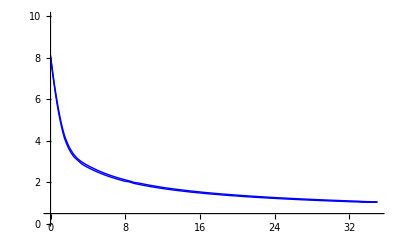

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[omchi1d[[All,{1,2}]],First]
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[omchi1d[[All,{1,2}]],First]
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->2];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->2];
figs1=Show[Plot[{Fb1[m],Fb2[m]},{m,0,35},PlotRange->{.1,10},PlotStyle->{Blue,Blue},Filling->{1->{2}}]]
```

{{44.,1.04543},{44.5,1.04522},{45.,1.04522},{45.5,1.04539}}

{{44.,1.17416},{44.5,1.18972},{45.,1.1966},{45.5,1.04717}}

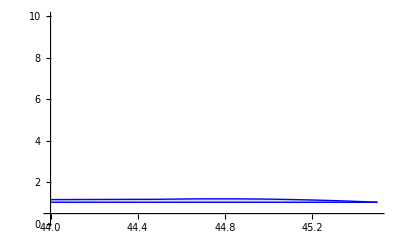

```mathematica
Lz1=(First[SortBy[#1,Last]]&)/@SplitBy[omchiz[[All,{1,2}]],First]
Lz2=(Last[SortBy[#1,Last]]&)/@SplitBy[omchiz[[All,{1,2}]],First]
Fz1=Interpolation[Lz1[[All,{1,2}]],InterpolationOrder->2];
Fz2=Interpolation[Lz2[[All,{1,2}]],InterpolationOrder->2];
figs1=Show[Plot[{Fz1[m],Fz2[m]},{m,44,45.5},PlotRange->{.1,10},PlotStyle->{Blue,Blue},Filling->{1->{2}}]]
```

{{54.5,1.04519},{55.,1.04519},{55.5,1.0452},{56.,1.04522},{56.5,1.04519},{57.,1.04523},{57.5,1.04522},{58.,1.04522},{58.5,1.04523},{59.,1.04519},{59.5,1.04522},{60.,1.04519},{60.5,1.04518},{61.,1.04517},{61.5,1.04518},{62.,1.04519},{62.5,1.04521},{63.,1.04517},{64.,1.04519},{65.,1.04518},{66.,1.0452},{67.,1.04518},{68.,1.04519},{69.,1.04523},{70.,1.04523},{71.,1.0452},{72.,1.04518},{73.,1.04519},{74.,1.04522},{75.,1.04522},{76.,1.04523},{77.,1.0452},{78.,1.04519},{79.,1.04519},{80.,1.04521},{81.,1.05258},{82.,1.06385},{83.,1.07423},{84.,1.08322},{85.,1.08871},{86.,1.09514},{87.,1.10357},{88.,1.11273},{89.,1.11277},{90.,1.12388},{95.,1.13826},{100.,1.15663},{105.,1.15664},{110.,1.18107},{115.,1.1811},{120.,1.18109},{125.,1.18111},{130.,1.18112},{135.,1.18107},{140.,1.18112},{145.,1.18107},{150.,1.18111},{165.,1.15663},{170.,1.15663},{175.,1.15662},{180.,1.15659},{185.,1.15662},{190.,1.15662},{195.,1.1566},{200.,1.41727}}

{{54.5,1.05757},{55.,2.03986},{55.5,1.52481},{56.,2.21834},{56.5,4.41106},{57.,6.60045},{57.5,8.78549},{58.,12.0643},{58.5,16.4314},{59.,20.7923},{59.5,26.2397},{60.,32.7714},{60.5,38.2036},{61.,43.6288},{61.5,45.779},{62.,41.3944},{62.5,1.52482},{63.,1.21554},{64.,1.35311},{65.,1.35309},{66.,1.35311},{67.,1.35309},{68.,1.35311},{69.,1.35316},{70.,1.26731},{71.,1.26727},{72.,1.26725},{73.,1.26726},{74.,1.2673},{75.,1.26729},{76.,1.21559},{77.,1.21556},{78.,1.21555},{79.,1.21555},{80.,1.21558},{81.,1.18109},{82.,1.18108},{83.,1.1811},{84.,2.15391},{85.,1.18111},{86.,1.1811},{87.,1.18111},{88.,1.18107},{89.,1.18111},{90.,1.1811},{95.,1.18109},{100.,1.18111},{105.,1.18111},{110.,1.18107},{115.,1.1811},{120.,1.18109},{125.,2.02969},{130.,1.18112},{135.,1.18107},{140.,1.68973},{145.,1.68966},{150.,1.18111},{165.,1.51972},{170.,1.51972},{175.,1.5197},{180.,1.15659},{185.,2.53454},{190.,1.15662},{195.,1.41725},{200.,1.41727}}

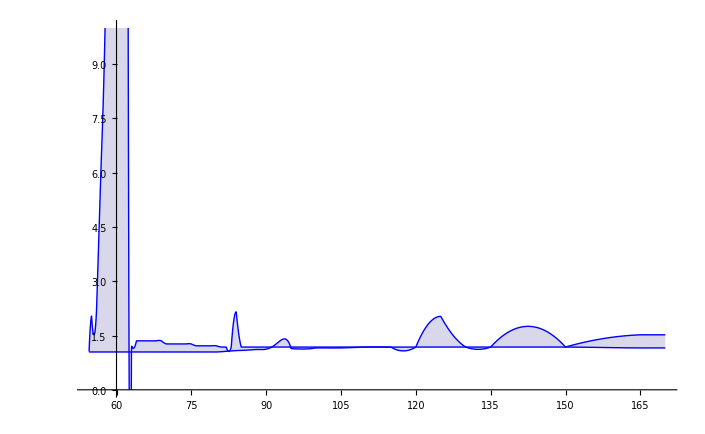

```mathematica
lo2=(First[SortBy[#1,Last]]&)/@SplitBy[omchi2[[All,{1,2}]],First]
lo22=(Last[SortBy[#1,Last]]&)/@SplitBy[omchi2[[All,{1,2}]],First]
fi2=Interpolation[lo2[[All,{1,2}]],InterpolationOrder->5];
fi22=Interpolation[lo22[[All,{1,2}]],InterpolationOrder->2];
figs1=Show[Plot[{fi2[m],fi22[m]},{m,54.5,170},PlotRange->{0,10},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

```mathematica
Higgs constraints
```

constraints Higgs

```mathematica
Lamm[mu3_,zz3_,mps_,Laff_]:=1000 Laff*zz3*mu3 Sqrt[2]/(Sqrt[1+((10+mps))^2/mps^2]vev);
```

```mathematica
RegHinv[lxx_,lamm_,mss_]:=(vev/(lamm))*((.014)*4*lamm^2/vev^2+lxx 4 Log[lamm/mss]);
```

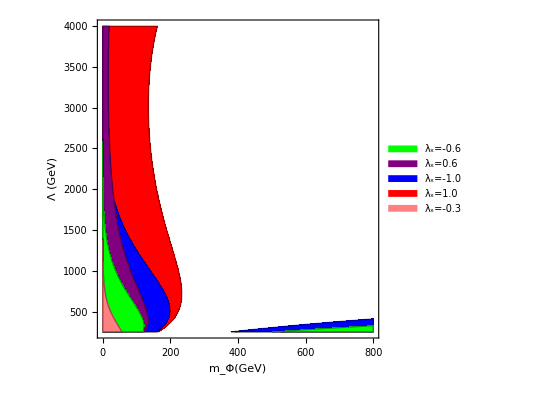

```mathematica
regH=Show[RegionPlot[Abs[RegHinv[1,la,mss]]>1.7,{mss,.1,800},{la,250,4000},PlotStyle->Red,PlotLegends->Placed[SwatchLegend[{Red},{"λ_x=1.0"},LabelStyle->16],{0.52,.85}]],RegionPlot[Abs[RegHinv[-1,la,mss]]>1.7,{mss,.1,800},{la,250,4000},PlotStyle->Blue,PlotLegends->Placed[SwatchLegend[{Blue},{"λ_x=-1.0"},LabelStyle->16],{0.52,.75}]],RegionPlot[Abs[RegHinv[.6,la,mss]]>1.7,{mss,.1,800},{la,250,4000},PlotStyle->Purple,PlotLegends->Placed[SwatchLegend[{Purple},{"λ_x=0.6"},LabelStyle->16],{0.52,.65}]],RegionPlot[Abs[RegHinv[-.6,la,mss]]>1.7,{mss,.1,800},{la,250,4000},PlotStyle->Green,PlotLegends->Placed[SwatchLegend[{Green},{"λ_x=-0.6"},LabelStyle->16],{0.52,.55}]],RegionPlot[Abs[RegHinv[-.3,la,mss]]>1.7,{mss,.1,800},{la,250,4000},PlotStyle->Pink,PlotLegends->Placed[SwatchLegend[{Pink},{"λ_x=-0.3"},LabelStyle->16],{0.52,.45}]],Frame->True,FrameLabel->{"m_Φ(GeV)","Λ (GeV)"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["RegHinv.pdf",regH]
```

RegHinv.pdf

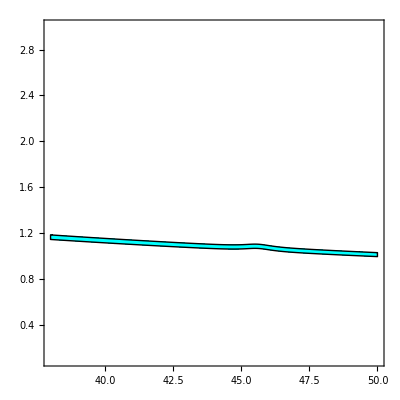

```mathematica
RegionPlot[0.1198-3 0.0026<Ω[(10+mfe)*1,1000]<0.1198+3 0.0026,{mfe,38,50},{Liff,.1,3},PlotPoints->100,PlotStyle->Cyan,BoundaryStyle->Directive[ Thin]]
```

```mathematica
fig4=Show[
RegionPlot[RegZinv[(mfe*1.01)]>.014,{mfe,1,80},{Liff,.5,15},PlotStyle->Purple,BoundaryStyle->Directive[Purple, Thin]],
ListPlot[{omchi1,omchi1d,omchi2,omchi2d,omchiz,omchizd},PlotStyle->{RGBColor[0,0.62,0.76],Red,RGBColor[0,0.62,0.76],Red,RGBColor[0,0.62,0.76],Red},PlotStyle->PointSize[Tiny],PlotLegends->Placed[PointLegend[{{RGBColor[0,0.62,0.76]},{Red}},{{"m_Φ=10+m_Ψ"},{"m_Φ=1.01m_Ψ"}},LabelStyle->12],{0.15,.9}]],
(*Plot[{fi2[m],fi22[m]},{m,54.5,200},PlotRange->{.1,10},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]]*)
(*Plot[{Fb1[m],Fb2[m]},{m,1,35},PlotRange->{.1,10},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],
Plot[{Fz1[m],Fz2[m]},{m,44,45.5},PlotRange->{.1,10},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],*)(*ListPlot[{omchi1},PlotRange->{{1,70},{.1,10}},PlotStyle->PointSize[.002]],ListPlot[{omchi2},PlotStyle->PointSize[.002]],*)
RegionPlot[RegZinv[(mfe+10)*1]>.0139,{mfe,1,80},{Liff,.5,15},(*Mesh->50,MeshFunctions->{#1-#2&},MeshShading->{None},*)PlotStyle->{Gray,Opacity[.6]},BoundaryStyle->Directive[Gray, Thin]],
RegionPlot[0.1198-3 0.0026<Ω[(mfe+10)*1,2670]<0.1198+3 0.0026,{mfe,.1,48},{Liff,.1,15},PlotPoints->300,PlotStyle->Red,BoundaryStyle->Directive[ Thin]],
RegionPlot[RegZinv[(mfe*1.01)]>.014,{mfe,1,80},{Liff,.5,15},PlotStyle->Purple,BoundaryStyle->Directive[Purple, Thin]],
Frame->True,FrameLabel->{"m_Ψ(GeV)","Λ_eff (TeV)"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

-Graphics-

```mathematica
Export["Leffmpsi3.png",fig4]
```

Leffmpsi3.png

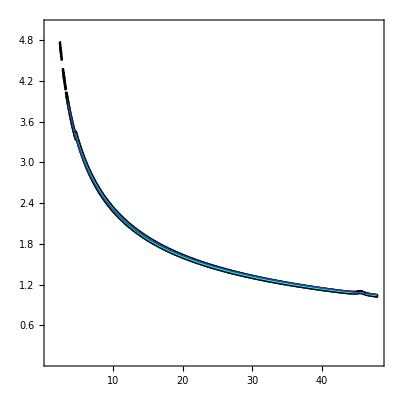

```mathematica
Show[RegionPlot[0.1198-3 0.0026<Ω[(mfe+10)*1,2000]<0.1198+3 0.0026,{mfe,1,48},{Liff,.1,5},PlotPoints->100,PlotStyle->Red,BoundaryStyle->Directive[ Thin]],
RegionPlot[0.1198-3 0.0026<Ω[1.01mfe,2000]<0.1198+3 0.0026,{mfe,.1,48},{Liff,.1,5},PlotPoints->100,PlotStyle->Cyan,BoundaryStyle->Directive[ Thin]],Plot[Sqrt[53/mf],{mf,1,48}]]
```

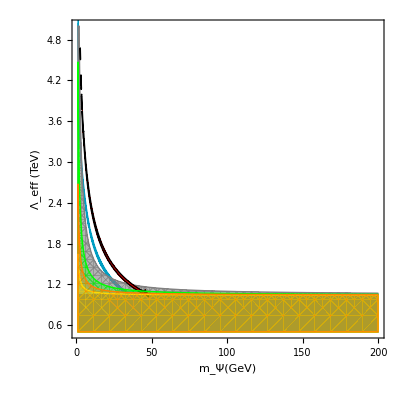

```mathematica
Zregs=Show[
RegionPlot[RegZinv[(mfe*1.01)]>.014,{mfe,1,200},{Liff,.5,5},PlotStyle->Purple,BoundaryStyle->Directive[Purple, Thin]],
(*Plot[{fi2[m],fi22[m]},{m,54.5,200},PlotRange->{.1,10},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]]*)
(*Plot[{Fb1[m],Fb2[m]},{m,1,35},PlotRange->{.1,10},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],
Plot[{Fz1[m],Fz2[m]},{m,44,45.5},PlotRange->{.1,10},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],*)(*ListPlot[{omchi1},PlotRange->{{1,70},{.1,10}},PlotStyle->PointSize[.002]],ListPlot[{omchi2},PlotStyle->PointSize[.002]],*)
Plot[{Fb1[m],Fb2[m]},{m,1,35},PlotRange->{.1,10},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],
RegionPlot[RegZinv[(mfe+10)*1]>.0139,{mfe,1,200},{Liff,.5,5},(*Mesh->50,MeshFunctions->{#1-#2&},MeshShading->{None},*)PlotStyle->{Gray,Opacity[.6]},BoundaryStyle->Directive[Gray, Thin]],
RegionPlot[0.1198-3 0.0026<Ω[(mfe+10)*1,2670]<0.1198+3 0.0026,{mfe,.1,48},{Liff,.1,5},PlotPoints->100,PlotStyle->Red,BoundaryStyle->Directive[ Thin]],
RegionPlot[RegZinv[mfe+5]>.014,{mfe,1,200},{Liff,.5,5},PlotStyle->Directive[Opacity[.3],Green],BoundaryStyle->Directive[Green, Thin]],
RegionPlot[RegZinv[mfe+1]>.014,{mfe,1,200},{Liff,.5,5},PlotStyle->Directive[Opacity[.3],Yellow],BoundaryStyle->Directive[Yellow, Thin]],
RegionPlot[RegZinv[mfe+2.5]>.014,{mfe,1,200},{Liff,.5,5},PlotStyle->Directive[Opacity[.3],Orange],BoundaryStyle->Directive[Orange, Thin]],
Frame->True,FrameLabel->{"m_Ψ(GeV)","Λ_eff (TeV)"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["LeffZregs.png",Zregs]
```

LeffZregs.png

Minimum Leff ~1.6 TeV

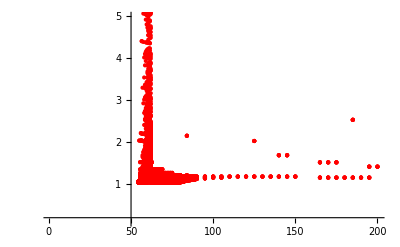

```mathematica
fig5=ListPlot[{omchi2},PlotRange->{{1,200},{.1,5}},PlotStyle->Red]
```

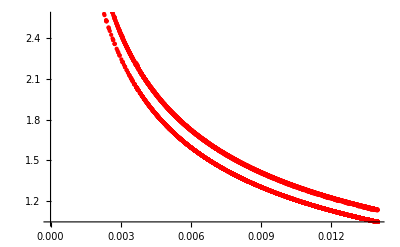

```mathematica
ListPlot[{omchi22},PlotStyle->Red]
```

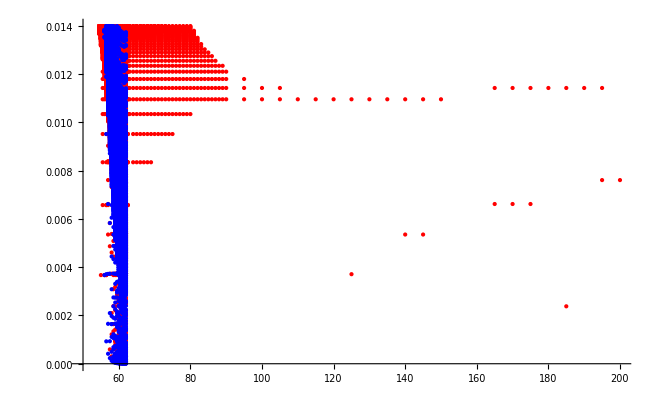

```mathematica
etams=ListPlot[{MfEta2,MfEta1},PlotRange->{{50,200},Automatic},PlotStyle->{Red,Blue}]
```

```mathematica
Export["Etavsmf.pdf",etams]
```

Etavsmf.pdf

```mathematica
Export["Leffvsmpsi3.png",fig4]
```

Leffvsmpsi3.png

```mathematica
RegZinv[mphi_]:=vev^2/(8*(Liff*1000)^2)(1+mphi^2/mfe^2)
```

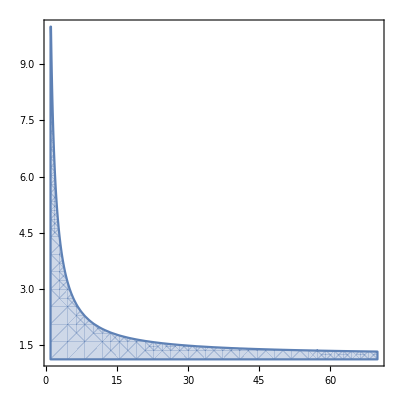

```mathematica
RegionPlot[RegZinv[(mfe+10)*1.33]>.014,{mfe,1,70},{Liff,1.13,10}]
```

Direct Detection

```mathematica
Region compatible with Planck and Lux
```

```mathematica
Get["/home/vanniagm/Dropbox/nu_portal/MATH_NUMODEL/xenon1T_lux15.m"]
```

InterpolatingFunction::dmval: Input value {605.825} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {546.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {646.629} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

/home/vanniagm/Dropbox/nu_portal

```mathematica
ptsAbLuxND=Table[If[om1[[i,10]]<lux15[om1[[i,1]]],om1[[i]],Unevaluated[Sequence[]]],{i,1,Length[om1]}];
```

InterpolatingFunction::dmval: Input value {561.617} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
ptsAbLuxND2=Table[If[om2[[i,10]]<lux15[om2[[i,1]]],om2[[i]],Unevaluated[Sequence[]]],{i,1,Length[om2]}];
```

```mathematica
ptsAbLuxD=Table[If[om1d[[i,10]]<lux15[om1d[[i,1]]],om1d[[i]],Unevaluated[Sequence[]]],{i,1,Length[om1d]}];
```

InterpolatingFunction::dmval: Input value {417.128} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
ptsAbLuxD2=Table[If[om2d[[i,10]]<lux15[om2d[[i,1]]],om2d[[i]],Unevaluated[Sequence[]]],{i,1,Length[om2d]}];
```

InterpolatingFunction::dmval: Input value {1236.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
ptsAbLuxD[[Length[ptsAbLuxD]]]
```

{31.5,1091.,121.2,121.2,-0.6,0.7666,0.12461,1.8749×10^-45,3.9116×10^-46,2.9923×10^-46,1.2777×10^8,0.089485,1.4316,2.402,0.0075281,0.1964}

{2.,1091.,36.36,36.36,0.,0.1683,0.1276,3.7836×10^-47,6.9231×10^-50,1.23×10^-47,24108.,3.9411×10^-8,0.000015981,2.4094,0.0060499,0.00005106}

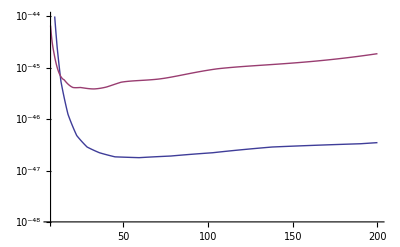

```mathematica
LogPlot[{xenon1t[m],lux15[m]},{m,7,200},PlotRange->{10^-48,10^-44}]
```

```mathematica
clxms1=Table[If[om1[[i,6]]<1,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
clxms2=Table[If[om1[[i,6]]==1,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
```

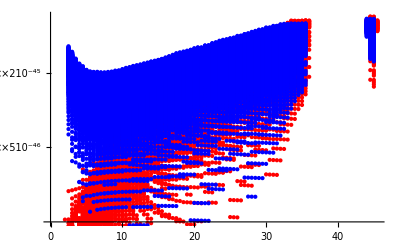

```mathematica
ListLogPlot[{clxms1,clxms2},PlotStyle->{Red,Blue}]
```

```mathematica
clxlx1=Table[If[om1[[i,5]]>0,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
clxlx2=Table[If[om1[[i,5]]<0,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
```

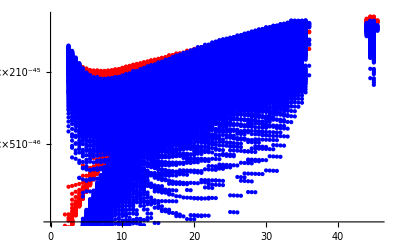

```mathematica
ListLogPlot[{clxlx1,clxlx2},PlotStyle->{Red,Blue}]
```

```mathematica
clxla1=Table[If[om1[[i,2]]>1000,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
clxla2=Table[If[om1[[i,2]]<1000,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
```

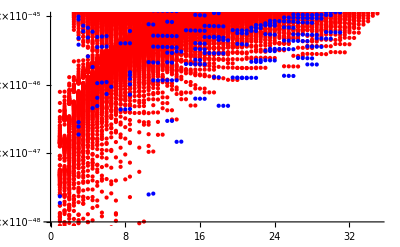

```mathematica
ListLogPlot[{clxla1,clxla2},PlotStyle->{Red,Blue},PlotRange->{{0,35},{10^-48,10^-45}}]
```

```mathematica
Sqrt[.014]
```

0.118322

```mathematica
omdd=Join[om1,om2];
ms11=Table[If[om1[[i,6]]<1&&om1[[i,1]]<40,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
ms12=Table[If[om1[[i,6]]==1&&om1[[i,1]]<40,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
ms21=Table[If[om2[[i,6]]<1,{om2[[i,1]],om2[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om2]}];
ms22=Table[If[om2[[i,6]]==1&&om2[[i,1]]≠84,{om2[[i,1]],om2[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om2]}];
```

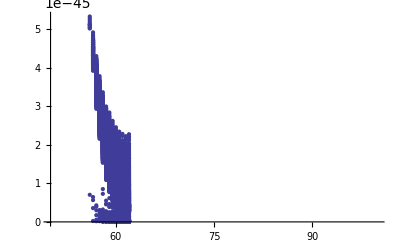

```mathematica
ListPlot[ms22,PlotRange->{{50,100},Automatic}]
```

```mathematica
msz1=Table[If[omz[[i,6]]<1,{omz[[i,1]],omz[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[omz]}];
msz2=Table[If[omz[[i,6]]==1,{omz[[i,1]],omz[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[omz]}];
```

```mathematica
sigeta=Table[If[omdd[[i,6]]<1&&omdd[[i,5]]==-.6,{(omdd[[i,3]]/omdd[[i,2]])^2,omdd[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[omdd]}];
sigeta2=Table[If[omdd[[i,6]]<1&&omdd[[i,5]]==-.3&&omdd[[i,2]]<6400,{(omdd[[i,3]]/omdd[[i,2]])^2,omdd[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[omdd]}]
sigeta22=Table[If[omdd[[i,6]]<1&&omdd[[i,5]]==-.3&&omdd[[i,2]]>6400,{(omdd[[i,3]]/omdd[[i,2]])^2,omdd[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[omdd]}]
sigeta3=Table[If[omdd[[i,6]]<1&&omdd[[i,5]]==0.,{(omdd[[i,3]]/omdd[[i,2]])^2,omdd[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[omdd]}];
sigeta4=Table[If[omdd[[i,6]]<1&&omdd[[i,5]]==.3,{(omdd[[i,3]]/omdd[[i,2]])^2,omdd[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[omdd]}]
```

{{0.000597896,3.1622×10^-47},{0.000598299,1.556×10^-47},{0.000598738,8.2888×10^-48},{0.000598866,4.5527×10^-48},{0.000598958,2.4894×10^-48},{0.000599026,1.3079×10^-48},{0.000570176,1.3504×10^-48},{0.00059919,6.2835×10^-49},{0.000573432,6.6653×10^-49},«4256»,{0.0134767,2.9827×10^-45},{0.0139703,3.2149×10^-45},{0.0135008,3.0356×10^-45},{0.0139864,3.2674×10^-45},{0.0135242,3.0884×10^-45},{0.0135468,3.141×10^-45},{0.0135725,3.1936×10^-45},{0.0135937,3.246×10^-45},{0.0136142,3.2983×10^-45}}

{{0.000599626,2.1615×10^-50},{0.000581596,1.3589×10^-50},{0.000599476,9.8183×10^-50},{0.000582711,7.9923×10^-50},{0.000599346,2.1403×10^-49},{0.00058368,1.8667×10^-49},{0.000599233,3.5751×10^-49},{0.00058453,3.2209×10^-49},{0.000570362,2.8986×10^-49},{0.000599714,5.2058×10^-49},«6307»,{0.0132196,4.4822×10^-45},{0.0135026,4.6824×10^-45},{0.0138126,4.8892×10^-45},{0.0132339,4.5338×10^-45},{0.0135378,4.7341×10^-45},{0.0138213,4.9409×10^-45},{0.013271,4.5855×10^-45},{0.013549,4.7858×10^-45},{0.0138298,4.9926×10^-45}}

{{0.000597896,7.9252×10^-47},{0.000598299,5.4504×10^-47},{0.000598738,4.1617×10^-47},{0.000598866,3.3919×10^-47},{0.000598958,2.8894×10^-47},{0.000599026,2.5407×10^-47},{0.000570176,2.3906×10^-47},{0.00059919,2.2876×10^-47},{0.000573432,2.1644×10^-47},{0.000599024,2.0976×10^-47},«10167»,{0.0138126,5.3048×10^-45},{0.0129566,4.7287×10^-45},{0.0132339,4.9311×10^-45},{0.0135378,5.1398×10^-45},{0.0138213,5.3552×10^-45},{0.0129732,4.7793×10^-45},{0.013271,4.9817×10^-45},{0.013549,5.1904×10^-45},{0.0138298,5.4056×10^-45}}

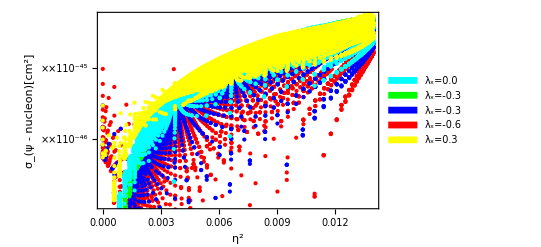

```mathematica
sigetafig=Show[ListLogPlot[{sigeta},PlotStyle->{Red},PlotLegends->Placed[SwatchLegend[{Red},{"λ_x=-0.6"},LabelStyle->16],{0.12,.85}]],
ListLogPlot[{sigeta2},PlotStyle->{Blue},PlotLegends->Placed[SwatchLegend[{Blue},{"λ_x=-0.3"},LabelStyle->16],{0.12,.75}]],
ListLogPlot[{sigeta22},PlotStyle->{Green},PlotLegends->Placed[SwatchLegend[{Green},{"λ_x=-0.3"},LabelStyle->16],{0.12,.65}]],
ListLogPlot[{sigeta3},PlotStyle->{Cyan},PlotLegends->Placed[SwatchLegend[{Cyan},{"λ_x=0.0"},LabelStyle->16],{0.12,.55}]],
ListLogPlot[{sigeta4},PlotStyle->{Yellow},PlotLegends->Placed[SwatchLegend[{Yellow},{"λ_x=0.3"},LabelStyle->16],{0.12,.45}]],Frame->{True},
FrameLabel->{"η^2","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)[\!\(\*SuperscriptBox[\(cm\), \(2\)]\)]"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["DD_mudep.pdf",sigetafig]
```

DD_mudep.pdf

```mathematica
Zsig[mmu_,lam_]:=(mu/lam)^2*4(1+Log[lam/1.01])
```

```mathematica
Hsig[mmu_,lam_,lx_]:=2*(246/lam)((mu/lam)^2*4*lam^2/246^2+lx 4 Log[lam/1.01])
```

```mathematica
230.3,1.4149
```

```mathematica
Hsig[145.5,6040,-.3]
Hsig[145.5,6040,.3]
```

-0.844007

0.856074

```mathematica
Zsig[145.5,6040]
```

0.00119135

```mathematica
Hsig[36.36,1487,-.3]
```

-2.87173

```mathematica
Zsig[157.6,6436]
```

0.00105613

```mathematica
clx6=Table[If[om1[[i,5]]<=-.3&&om1[[i,6]]==1&&om1[[i,2]]==1000,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}]
```

{}

```mathematica
clx6II={{4.,2.6606*^-46},{5.,2.1336*^-46},{12.,1.7062*^-46},{19.,2.9297*^-46},{22.,3.6744*^-46},{25.,4.5129*^-46},{32.,2.7352*^-46},{35.,3.5583*^-46}}
```

{{4.,2.6606×10^-46},{5.,2.1336×10^-46},{12.,1.7062×10^-46},{19.,2.9297×10^-46},{22.,3.6744×10^-46},{25.,4.5129×10^-46},{32.,2.7352×10^-46},{35.,3.5583×10^-46}}

```mathematica
Export["LimInfDD.dat",clx6II]
```

LimInfDD.dat

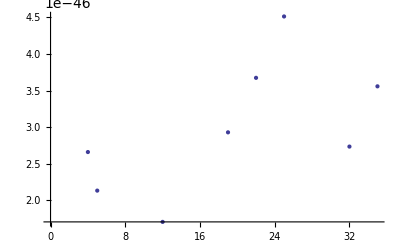

```mathematica
ListPlot[clx6II]
```

```mathematica
clx=Interpolation[clx6II,InterpolationOrder->5]
```

InterpolatingFunction[{{4.,35.}},<>]

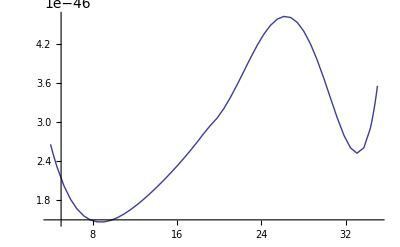

```mathematica
Plot[clx[mfe],{mfe,4,35}]
```

```mathematica
sigmpsinoncoh=Table[{om1[[i,1]],om1[[i,10]]},{i,1,Length[om1]}];
sigmpsinoncoh2=Table[{om2[[i,1]],om2[[i,10]]},{i,1,Length[om2]}];
```

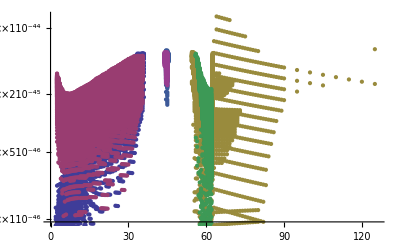

```mathematica
ListLogPlot[{ms11,ms12,ms21,ms22,msz1,msz2}]
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[ms11[[All,{1,2}]],First]
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[ms11[[All,{1,2}]],First]
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->1];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->1]
```

{{1.,1.6238×10^-51},{1.5,1.7406×10^-51},{2.,2.3952×10^-53},{2.5,8.3459×10^-57},{3.,8.8537×10^-52},{3.5,1.0935×10^-52},{4.,9.8303×10^-51},{4.5,6.9553×10^-51},{5.,9.7809×10^-50},{5.5,2.3648×10^-51},{6.,2.5219×10^-50},{6.5,7.491×10^-50},{7.,5.3984×10^-50},{7.5,3.1298×10^-49},{8.,2.7463×10^-49},{8.5,1.536×10^-52},{9.,3.8913×10^-47},{9.5,9.552×10^-49},{10.,1.0114×10^-48},{10.5,2.5163×10^-48},{11.,2.5891×10^-48},{11.5,1.8686×10^-47},{12.,1.8796×10^-47},{12.5,2.9853×10^-47},{13.,2.9854×10^-47},{13.5,1.477×10^-47},{14.,1.4851×10^-47},{14.5,6.1839×10^-47},{15.,5.0074×10^-47},{15.5,5.0077×10^-47},{16.,6.2981×10^-47},{16.5,6.2801×10^-47},{17.,7.7835×10^-47},{17.5,7.7724×10^-47},{18.,4.9669×10^-47},{18.5,4.9609×10^-47},{19.,4.9546×10^-47},{19.5,1.1858×10^-46},{20.,1.1829×10^-46},{20.5,1.262×10^-46},{21.,1.2567×10^-46},{21.5,2.1798×10^-46},{22.,1.7885×10^-46},{22.5,1.783×10^-46},{23.,1.7775×10^-46},{23.5,2.482×10^-46},{24.,2.4732×10^-46},{24.5,3.2142×10^-46},{25.,1.3611×10^-46},{25.5,1.3563×10^-46},{26.,1.3515×10^-46},{26.5,1.8581×10^-46},{27.,2.4676×10^-46},{27.5,2.4563×10^-46},{28.,2.4451×10^-46},{28.5,3.6145×10^-46},{29.,3.5968×10^-46},{29.5,4.7615×10^-46},{30.,3.0213×10^-46},{30.5,3.0115×10^-46},{31.,3.0019×10^-46},{31.5,2.9923×10^-46},{32.,3.9209×10^-46},{32.5,4.8561×10^-46},{33.,5.7849×10^-46},{33.5,7.6253×10^-46},{34.,8.5043×10^-46},{34.5,1.0235×10^-45},{35.,1.1051×10^-45},{35.5,1.3473×10^-45},{36.,1.8692×10^-45}}

{{1.,7.9252×10^-47},{1.5,7.9738×10^-47},{2.,1.2983×10^-46},{2.5,2.2091×10^-46},{3.,2.2453×10^-46},{3.5,2.2872×10^-46},{4.,2.3324×10^-46},{4.5,3.3221×10^-46},{5.,3.2257×10^-46},{5.5,4.0468×10^-46},{6.,3.8394×10^-46},{6.5,3.7028×10^-46},{7.,4.9395×10^-46},{7.5,4.6935×10^-46},{8.,5.2336×10^-46},{8.5,6.1221×10^-46},{9.,6.3165×10^-46},{9.5,6.9952×10^-46},{10.,7.4916×10^-46},{10.5,8.3013×10^-46},{11.,8.8561×10^-46},{11.5,9.7428×10^-46},{12.,1.0369×10^-45},{12.5,1.1038×10^-45},{13.,1.2057×10^-45},{13.5,1.2779×10^-45},{14.,1.3532×10^-45},{14.5,1.4316×10^-45},{15.,1.5224×10^-45},{15.5,1.6091×10^-45},{16.,1.6993×10^-45},{16.5,1.7782×10^-45},{17.,1.8736×10^-45},{17.5,1.9727×10^-45},{18.,2.0755×10^-45},{18.5,2.1822×10^-45},{19.,2.2929×10^-45},{19.5,2.4076×10^-45},{20.,2.4784×10^-45},{20.5,2.6008×10^-45},{21.,2.6782×10^-45},{21.5,2.8088×10^-45},{22.,2.8934×10^-45},{22.5,2.9816×10^-45},{23.,3.0736×10^-45},{23.5,3.1176×10^-45},{24.,3.2173×10^-45},{24.5,3.3216×10^-45},{25.,3.4217×10^-45},{25.5,3.5778×10^-45},{26.,3.6318×10^-45},{26.5,3.7435×10^-45},{27.,3.86×10^-45},{27.5,3.9271×10^-45},{28.,4.0336×10^-45},{28.5,4.1018×10^-45},{29.,4.2013×10^-45},{29.5,4.3849×10^-45},{30.,4.5189×10^-45},{30.5,4.5477×10^-45},{31.,4.647×10^-45},{31.5,4.7923×10^-45},{32.,4.944×10^-45},{32.5,4.9319×10^-45},{33.,5.1346×10^-45},{33.5,5.3492×10^-45},{34.,5.3368×10^-45},{34.5,5.3246×10^-45},{35.,5.3289×10^-45},{35.5,5.369×10^-45},{36.,5.3557×10^-45}}

InterpolatingFunction[{{1.,36.}},<>]

{{54.5,2.5684×10^-45},{55.,9.6073×10^-46},{55.5,2.3333×10^-49},{56.,2.0613×10^-49},{56.5,2.3185×10^-47},{57.,4.7776×10^-49},{57.5,2.6968×10^-47},{58.,3.6132×10^-48},{58.5,1.1021×10^-48},{59.,1.9606×10^-49},{59.5,4.7751×10^-49},{60.,1.2456×10^-49},{60.5,8.8026×10^-51},{61.,8.298×10^-50},{61.5,3.4362×10^-51},{62.,4.987×10^-50},{62.5,9.5797×10^-51},{63.,1.217×10^-49},{64.,1.6452×10^-49},{65.,2.1301×10^-49},{66.,2.6689×10^-49},{67.,3.2591×10^-49},{68.,3.8984×10^-49},{69.,4.5847×10^-49},{70.,5.3157×10^-49},{71.,6.0896×10^-49},{72.,6.9044×10^-49},{73.,7.7583×10^-49},{74.,8.6496×10^-49},{75.,9.5768×10^-49},{76.,8.9882×10^-49},{77.,7.9897×10^-49},{78.,7.0614×10^-49},{79.,6.2009×10^-49},{80.,5.4058×10^-49},{81.,4.6738×10^-49},{82.,5.112×10^-47},{83.,2.239×10^-46},{84.,4.4804×10^-46},{85.,6.0494×10^-46},{86.,8.0262×10^-46},{87.,1.0513×10^-45},{88.,1.3644×10^-45},{89.,1.3493×10^-45},{90.,1.7404×10^-45},{95.,2.1395×10^-45},{100.,2.6232×10^-45},{105.,2.483×10^-45},{110.,3.0308×10^-45},{115.,2.8673×10^-45},{120.,2.7149×10^-45},{125.,2.5724×10^-45},{130.,2.439×10^-45},{135.,2.3138×10^-45},{140.,2.1963×10^-45},{145.,2.0857×10^-45},{150.,1.9814×10^-45},{165.,1.3606×10^-45},{170.,1.2979×10^-45},{175.,1.2384×10^-45},{180.,1.1819×10^-45},{185.,1.1282×10^-45},{190.,1.0771×10^-45},{195.,1.0285×10^-45},{200.,1.5683×10^-45}}

{{54.5,5.5566×10^-45},{55.,5.5466×10^-45},{55.5,5.3837×10^-45},{56.,4.8354×10^-45},{56.5,4.2353×10^-45},{57.,3.703×10^-45},{57.5,3.2254×10^-45},{58.,2.8814×10^-45},{58.5,2.6311×10^-45},{59.,2.4577×10^-45},{59.5,2.3393×10^-45},{60.,2.2202×10^-45},{60.5,2.1001×10^-45},{61.,2.0375×10^-45},{61.5,2.033×10^-45},{62.,2.0285×10^-45},{62.5,5.4056×10^-45},{63.,7.2264×10^-45},{64.,1.3107×10^-44},{65.,1.2879×10^-44},{66.,1.2657×10^-44},{67.,1.2439×10^-44},{68.,1.2227×10^-44},{69.,1.2019×10^-44},{70.,8.731×10^-45},{71.,8.5989×10^-45},{72.,8.4695×10^-45},{73.,8.3428×10^-45},{74.,8.2187×10^-45},{75.,8.0971×10^-45},{76.,6.0017×10^-45},{77.,5.9201×10^-45},{78.,5.8402×10^-45},{79.,5.7617×10^-45},{80.,5.6847×10^-45},{81.,4.271×10^-45},{82.,4.2175×10^-45},{83.,4.1649×10^-45},{84.,4.1133×10^-45},{85.,4.0626×10^-45},{86.,4.0128×10^-45},{87.,3.9638×10^-45},{88.,3.9156×10^-45},{89.,3.8683×10^-45},{90.,3.8217×10^-45},{95.,3.6002×10^-45},{100.,3.3957×10^-45},{105.,3.2064×10^-45},{110.,3.0308×10^-45},{115.,2.8673×10^-45},{120.,2.7149×10^-45},{125.,5.9472×10^-45},{130.,2.439×10^-45},{135.,2.3138×10^-45},{140.,4.1408×10^-45},{145.,3.9018×10^-45},{150.,1.9814×10^-45},{165.,2.6259×10^-45},{170.,2.4942×10^-45},{175.,2.3696×10^-45},{180.,1.1819×10^-45},{185.,2.8263×10^-45},{190.,1.0771×10^-45},{195.,1.6419×10^-45},{200.,1.5683×10^-45}}

{{2.5,6.3725×10^-46},{3.,3.8731×10^-46},{3.5,3.7762×10^-46},{4.,2.613×10^-46},{4.5,1.8286×10^-46},{5.,1.0618×10^-46},{5.5,1.0841×10^-46},{6.,1.1021×10^-46},{6.5,1.5583×10^-46},{7.,1.5765×10^-46},{7.5,4.3667×10^-47},{8.,4.4104×10^-47},{8.5,4.448×10^-47},{9.,1.6224×10^-46},{9.5,1.0809×10^-46},{10.,1.0856×10^-46},{10.5,1.0895×10^-46},{11.,1.0927×10^-46},{11.5,1.0954×10^-46},{12.,1.0975×10^-46},{12.5,1.1685×10^-46},{13.,1.168×10^-46},{13.5,1.1672×10^-46},{14.,1.6437×10^-46},{14.5,2.0191×10^-46},{15.,1.6782×10^-46},{15.5,1.6772×10^-46},{16.,1.676×10^-46},{16.5,1.6746×10^-46},{17.,1.673×10^-46},{17.5,1.6711×10^-46},{18.,2.3278×10^-46},{18.5,2.3238×10^-46},{19.,2.3196×10^-46},{19.5,1.2822×10^-46},{20.,1.2797×10^-46},{20.5,1.277×10^-46},{21.,1.2744×10^-46},{21.5,1.2717×10^-46},{22.,1.2689×10^-46},{22.5,2.3012×10^-46},{23.,2.2937×10^-46},{23.5,2.2863×10^-46},{24.,2.2788×10^-46},{24.5,3.2455×10^-46},{25.,3.3454×10^-46},{25.5,3.3333×10^-46},{26.,3.3212×10^-46},{26.5,4.3928×10^-46},{27.,2.8493×10^-46},{27.5,1.9959×10^-46},{28.,1.9924×10^-46},{28.5,1.9888×10^-46},{29.,2.823×10^-46},{29.5,2.8164×10^-46},{30.,3.6754×10^-46},{30.5,4.5429×10^-46},{31.,4.5303×10^-46},{31.5,5.3917×10^-46},{32.,6.2431×10^-46},{32.5,7.0803×10^-46},{33.,8.73×10^-46},{33.5,1.0317×10^-45},{34.,1.1841×10^-45},{34.5,1.3307×10^-45},{35.,1.3999×10^-45},{35.5,1.6081×10^-45}}

{{2.5,3.3082×10^-45},{3.,2.9853×10^-45},{3.5,2.6295×10^-45},{4.,2.3972×10^-45},{4.5,2.2818×10^-45},{5.,2.1311×10^-45},{5.5,2.0708×10^-45},{6.,2.05×10^-45},{6.5,2.0537×10^-45},{7.,2.0372×10^-45},{7.5,2.0328×10^-45},{8.,2.0494×10^-45},{8.5,2.0633×10^-45},{9.,2.0996×10^-45},{9.5,2.1092×10^-45},{10.,2.1601×10^-45},{10.5,2.2101×10^-45},{11.,2.2432×10^-45},{11.5,2.2917×10^-45},{12.,2.3252×10^-45},{12.5,2.3598×10^-45},{13.,2.4072×10^-45},{13.5,2.4431×10^-45},{14.,2.4899×10^-45},{14.5,2.5275×10^-45},{15.,2.5671×10^-45},{15.5,2.6136×10^-45},{16.,2.6873×10^-45},{16.5,2.7494×10^-45},{17.,2.8202×10^-45},{17.5,2.9102×10^-45},{18.,2.9566×10^-45},{18.5,3.0005×10^-45},{19.,3.0471×10^-45},{19.5,3.0967×10^-45},{20.,3.194×10^-45},{20.5,3.2475×10^-45},{21.,3.2427×10^-45},{21.5,3.3594×10^-45},{22.,3.3619×10^-45},{22.5,3.5127×10^-45},{23.,3.5712×10^-45},{23.5,3.6704×10^-45},{24.,3.7332×10^-45},{24.5,3.7799×10^-45},{25.,3.8469×10^-45},{25.5,3.8936×10^-45},{26.,4.0183×10^-45},{26.5,4.0416×10^-45},{27.,4.1522×10^-45},{27.5,4.2233×10^-45},{28.,4.3306×10^-45},{28.5,4.4105×10^-45},{29.,4.514×10^-45},{29.5,4.5498×10^-45},{30.,4.7027×10^-45},{30.5,4.6951×10^-45},{31.,4.8428×10^-45},{31.5,4.8467×10^-45},{32.,4.9884×10^-45},{32.5,5.0338×10^-45},{33.,5.0254×10^-45},{33.5,5.0707×10^-45},{34.,5.0623×10^-45},{34.5,5.0539×10^-45},{35.,5.0507×10^-45},{35.5,5.0814×10^-45}}

{{56.,7.0331×10^-46},{56.5,2.3547×10^-47},{57.,1.7697×10^-47},{57.5,1.944×10^-47},{58.,1.745×10^-49},{58.5,3.5998×10^-49},{59.,9.6797×10^-49},{59.5,2.3379×10^-49},{60.,1.0803×10^-49},{60.5,5.292×10^-52},{61.,1.2744×10^-49},{61.5,9.5737×10^-52},{62.,5.2948×10^-50}}

{{56.,5.331×10^-45},{56.5,4.918×10^-45},{57.,4.3025×10^-45},{57.5,3.7821×10^-45},{58.,3.3635×10^-45},{58.5,2.9943×10^-45},{59.,2.8383×10^-45},{59.5,2.6209×10^-45},{60.,2.4552×10^-45},{60.5,2.3425×10^-45},{61.,2.2838×10^-45},{61.5,2.225×10^-45},{62.,2.2754×10^-45}}

{{44.,4.3074×10^-45},{44.5,1.7697×10^-45},{45.,1.5558×10^-45},{45.5,4.388×10^-45}}

{{44.,5.406×10^-45},{44.5,5.7756×10^-45},{45.,5.7637×10^-45},{45.5,5.3706×10^-45}}

{{44.,3.9555×10^-45},{44.5,2.6086×10^-45},{45.,2.4901×10^-45}}

{{44.,5.5363×10^-45},{44.5,5.5272×10^-45},{45.,5.5181×10^-45}}

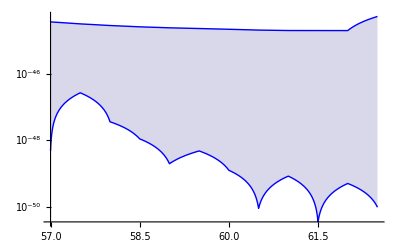

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[ms21[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[ms21[[All,{1,2}]],First]
fis2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fis22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];

me2=(First[SortBy[#1,Last]]&)/@SplitBy[ms12[[All,{1,2}]],First]
me22=(Last[SortBy[#1,Last]]&)/@SplitBy[ms12[[All,{1,2}]],First]
mis2=Interpolation[me2[[All,{1,2}]],InterpolationOrder->1];
mis22=Interpolation[me22[[All,{1,2}]],InterpolationOrder->1];

ne2=(First[SortBy[#1,Last]]&)/@SplitBy[ms22[[All,{1,2}]],First]
ne22=(Last[SortBy[#1,Last]]&)/@SplitBy[ms22[[All,{1,2}]],First]
nis2=Interpolation[ne2[[All,{1,2}]],InterpolationOrder->1];
nis22=Interpolation[ne22[[All,{1,2}]],InterpolationOrder->1];

oe2=(First[SortBy[#1,Last]]&)/@SplitBy[msz1[[All,{1,2}]],First]
oe22=(Last[SortBy[#1,Last]]&)/@SplitBy[msz1[[All,{1,2}]],First]
ois2=Interpolation[oe2[[All,{1,2}]],InterpolationOrder->1];
ois22=Interpolation[oe22[[All,{1,2}]],InterpolationOrder->1];

pe2=(First[SortBy[#1,Last]]&)/@SplitBy[msz2[[All,{1,2}]],First]
pe22=(Last[SortBy[#1,Last]]&)/@SplitBy[msz2[[All,{1,2}]],First]
pis2=Interpolation[pe2[[All,{1,2}]],InterpolationOrder->1];
pis22=Interpolation[pe22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

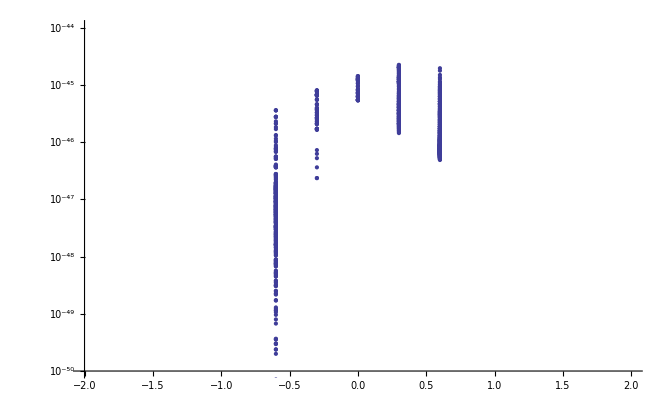

```mathematica
figlx=Show[ListLogPlot[{siglx},PlotRange->{{-2,2},{10^-50,10^-44}}]]
```

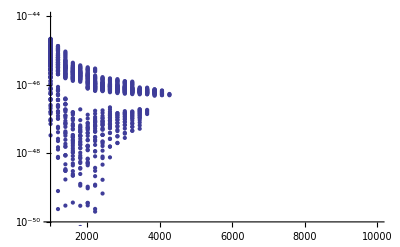

```mathematica
figlam=Show[ListLogPlot[{siglam},PlotRange->{{1000,10000},{10^-50,10^-44}}]]
```

InterpolatingFunction::dmval: Input value {591.081} lies outside the range of data in the interpolating function. Extrapolation will be used.

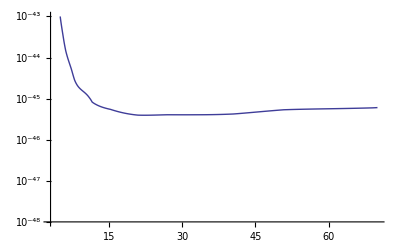

```mathematica
LogPlot[lux15[m],{m,3,70},PlotRange->{10.^-48,10.^-43}]
```

```mathematica
siglxvsmu=Table[{om[[i,1]],om[[i,5]]},{i,1,Length[om]}];
```

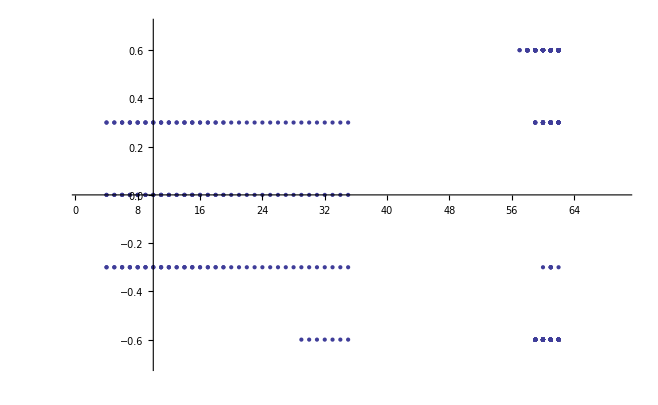

```mathematica
figlxvspars=Show[ListPlot[{siglxvsmu},PlotRange->{{1,70},{-.7,.7}}]]
```

```mathematica
tickSpecification=Table[{10^-(i),Superscript[10,-i]},{i,44,48}];
```

```mathematica
figsignocoh=Show[ListLogPlot[{sigmpsinoncoh},PlotRange->{{1,100},{10^-48,10^-44}},PlotStyle->Transparent,FrameTicks->Automatic],LogPlot[{Fb1[m],Fb2[m]},{m,1,36},PlotStyle->{None,None},Filling->{1->{2}},FillingStyle->{Cyan}],
LogPlot[{fis2[m],fis22[m]},{m,54.5,170},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->{Cyan}],
LogPlot[{mis2[m],mis22[m]},{m,2.5,35.5},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->{Lighter[Blue]}],
LogPlot[{nis2[m],nis22[m]},{m,56,62},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->{Lighter[Blue]}],
LogPlot[{ois2[m],ois22[m]},{m,44,45.5},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->{Cyan}],
LogPlot[{pis2[m],pis22[m]},{m,44,45},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->{Lighter[Blue]}],
LogPlot[σlux[m],{m,1,100},PlotStyle->{Green},PlotLegends->Placed[LineLegend[{Green},{"Lux 90% C.L. (2014)"},LabelStyle->16],{0.58,.52}]],
LogPlot[lux15[m],{m,1,100},PlotStyle->{Black},PlotRange->{10^-48,10^-44},PlotLegends->Placed[LineLegend[{Black},{"Lux 90% C.L. (2015)"},LabelStyle->16],{0.58,.52}]],
LogPlot[xenon1t[m],{m,1,100},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{Red,Dashed},{"Xenon1T"},LabelStyle->16],{0.58,.52}]],
(*LogPlot[Atlas[m],{m,4,63.5},PlotRange->{10.^-48,10.^-43},PlotStyle->{Red, Dashed},Frame->{True,True,False,False},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ψ\)]\) (GeV)","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)(\!\(\*SuperscriptBox[\(cm\), \(2\)]\))"},PlotLegends->Placed[LineLegend[{Red},{"Atlas 90% C.L. (2015)"},LabelStyle->12],{0.655,.77}]]*)Frame->True,FrameLabel->{"m_Ψ [GeV]","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)[\!\(\*SuperscriptBox[\(cm\), \(2\)]\)]"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
figsignocoh=Show[ListLogPlot[{Table[{om1[[i,1]],om1[[i,10]]},{i,1,Length[om1]}],Table[{om1d[[i,1]],om1d[[i,10]]},{i,1,Length[om1d]}],Table[{om2[[i,1]],om2[[i,10]]},{i,1,Length[om2]}],Table[{om2d[[i,1]],om2d[[i,10]]},{i,1,Length[om2d]}],Table[{omz[[i,1]],omz[[i,10]]},{i,1,Length[omz]}],Table[{omzd[[i,1]],omzd[[i,10]]},{i,1,Length[omzd]}]},PlotRange->{{1,80},{10^-48,10^-44}},PlotStyle->{RGBColor[0,0.62,0.76],Cyan,RGBColor[0,0.62,0.76],Cyan,RGBColor[0,0.62,0.76],Cyan},PlotStyle->PointSize[Tiny]],
LogPlot[σlux[m],{m,1,80},PlotStyle->{Green},PlotLegends->Placed[LineLegend[{Green},{"Lux 90% C.L. (2014)"},LabelStyle->16],{0.68,.52}]],
LogPlot[lux15[m],{m,4,80},PlotStyle->{Black},PlotRange->{10^-48,10^-44},PlotLegends->Placed[LineLegend[{Black},{"Lux 90% C.L. (2015)"},LabelStyle->16],{0.68,.52}]],
LogPlot[xenon1t[m],{m,7,80},PlotStyle->{Red,Dashed},PlotRange->{10^-48,10^-44},PlotLegends->Placed[LineLegend[{Red,Dashed},{"Xenon1T"},LabelStyle->16],{0.68,.52}]],
(*LogPlot[Atlas[m],{m,4,63.5},PlotRange->{10.^-48,10.^-43},PlotStyle->{Red, Dashed},Frame->{True,True,False,False},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ψ\)]\) (GeV)","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)(\!\(\*SuperscriptBox[\(cm\), \(2\)]\))"},PlotLegends->Placed[LineLegend[{Red},{"Atlas 90% C.L. (2015)"},LabelStyle->12],{0.655,.77}]]*)Frame->True,FrameLabel->{"m_Ψ [GeV]","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)[\!\(\*SuperscriptBox[\(cm\), \(2\)]\)]"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

InterpolatingFunction::dmval: Input value {344.688} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Export["DDincoherent.png",figsignocoh]
```

DDincoherent.png

```mathematica
ptsAbLuxND[[2]]
```

{2.5,9.8076×10^-46}

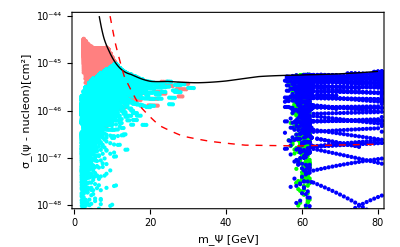

```mathematica
figsignocoh2=Show[ListLogPlot[{Table[{ptsAbLuxND[[i,1]],ptsAbLuxND[[i,10]]},{i,1,Length[ptsAbLuxND]}],Table[{ptsAbLuxND2[[i,1]],ptsAbLuxND2[[i,10]]},{i,1,Length[ptsAbLuxND2]}],Table[{ptsAbLuxD[[i,1]],ptsAbLuxD[[i,10]]},{i,1,Length[ptsAbLuxD]}],Table[{ptsAbLuxD2[[i,1]],ptsAbLuxD2[[i,10]]},{i,1,Length[ptsAbLuxD2]}]},PlotRange->{{1,80},{10^-48,10^-44}},PlotStyle->{Pink,Green,Cyan,Blue},PlotStyle->PointSize[Tiny]],
LogPlot[lux15[m],{m,4,80},PlotStyle->{Black},PlotRange->{10^-48,10^-44},PlotLegends->Placed[LineLegend[{Black},{"Lux 90% C.L. (2015)"},LabelStyle->16],{0.68,.52}]],
LogPlot[xenon1t[m],{m,7,80},PlotStyle->{Red,Dashed},PlotRange->{10^-48,10^-44},PlotLegends->Placed[LineLegend[{Red,Dashed},{"Xenon1T"},LabelStyle->16],{0.68,.52}]],
(*LogPlot[Atlas[m],{m,4,63.5},PlotRange->{10.^-48,10.^-43},PlotStyle->{Red, Dashed},Frame->{True,True,False,False},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ψ\)]\) (GeV)","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)(\!\(\*SuperscriptBox[\(cm\), \(2\)]\))"},PlotLegends->Placed[LineLegend[{Red},{"Atlas 90% C.L. (2015)"},LabelStyle->12],{0.655,.77}]]*)Frame->True,FrameLabel->{"m_Ψ [GeV]","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)[\!\(\*SuperscriptBox[\(cm\), \(2\)]\)]"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["DDincoherent.png",figsignocoh2]
```

DDincoherent.png

```mathematica
Export["DD_PlanckLux15_ND1.dat",ptsAbLuxND]
```

DD_PlanckLux15_ND1.dat

```mathematica
Export["DD_PlanckLux15_ND2.dat",ptsAbLuxND2]
```

DD_PlanckLux15_ND2.dat

```mathematica
Export["DD_PlanckLux15_D1.dat",ptsAbLuxD]
```

DD_PlanckLux15_D1.dat

```mathematica
Export["DD_PlanckLux15_D2.dat",ptsAbLuxD2]
```

DD_PlanckLux15_D2.dat

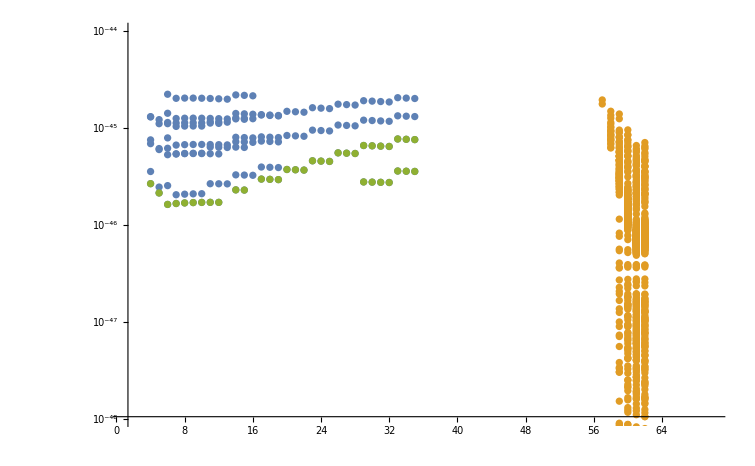

```mathematica
ListLogPlot[{sigmpsinoncoh,sigmpsinoncoh2,clx6},PlotRange->{{1,70},{10^-48,10^-44}}]
```

```mathematica
ListPlot3D[{sigmpsinoncoh3},PlotRange->{{1,28},{1000,1200},{0,2}}]
```

-Graphics3D-

List in order : Mpsi,  Lam,  mu (1), mu (3), Lx, kk, Om, SigmaPsiP, SigmaPsiN, SigTotIncoh, NuFlux from Sun, MuonFlux Upward, MuonFlux Contained, Z width, H width, HBR inv

Indirect Detection

```mathematica
vev=246.;
MH=125.7;
MZ=91.1876;
MW=80.401;
GZ=2.49;
GH=.004;
mτ=1.77682;
MTA=mτ;
mt=173.21;
MB=4.66;
(*cviiR=-10.;
cviiL=-8;*)
cw=MW/MZ;
gew=2*MW/vev;
gLmRb=-1+4/3 (cw^2-1);
gzz=gew/(4 Pi cw);
(*ciii=1.5;
cii=.1;*)
w=ArcCos[80.385/91.1876];
```

```mathematica
gevI2cm2=0.3894*10^(-27)2.9979*10^10;
```

```mathematica
svnn[mpsi_,mudm1_,mphi_,Lam_]:=gevI2cm2 2^4 mpsi^2 mudm1^4/(64 (mphi^2+mpsi^2)^2 Pi Lam^4 )
```

```mathematica
svnn2[mpsi_,etasq_,mphi_]:=gevI2cm2 2^4 mpsi^2 etasq^2/(64 (mphi^2+mpsi^2)^2 Pi )
```

```mathematica
Solve[svnn2[.1,x,(10+.1)*1]==3*10^-26,x]
```

{{x→-0.183335},{x→0.183335}}

```mathematica
Solve[svnn[1,.001*x^2,11,x]==3.*10^-26,x]
```

{{x→-148.067},{x→0.-148.067 ⅈ},{x→0.+148.067 ⅈ},{x→148.067}}

```mathematica
(gz^4 Sqrt[1-MB^2/mpsi^2] mpsi^2 Nf zi2di2^2 (1/4 (1+gLmGr^2+((-3+gLmGr^2) MB^2)/(2 mpsi^2)) Log[Λ/mphi]+(1/8 (1+gLmGr^2)+((-1+gLmGr^2) MB^2)/(16 mpsi^2)) (1+Log[Λ/mphi]^2)))/(64 (16 mpsi^4+Gz^2 MZ^2-8 mpsi^2 MZ^2+MZ^4) π )
```

(gz^4 √(1-21.7156/mpsi^2) mpsi^2 Nf zi2di2^2 (1/4 (1+gLmGr^2+(10.8578 (-3+gLmGr^2))/mpsi^2) Log[Λ/mphi]+(1/8 (1+gLmGr^2)+(1.35723 (-1+gLmGr^2))/mpsi^2) (1+Log[Λ/mphi]^2)))/(64 (6.91422×10^7+8315.18 Gz^2-66521.4 mpsi^2+16 mpsi^4) π)

```mathematica
svffZ[mpsi_,Lam_,mu3_,mphi_,z_,MB_,gLmGr_,Nf_]:=gevI2cm2(gzz^4 Sqrt[1-MB^2/mpsi^2] mpsi^2 Nf (z*mu3/Lam)^4 (1/4 (1+gLmGr^2+((-3+gLmGr^2) MB^2)/(2 mpsi^2)) Log[Lam/mphi]+(1/8 (1+gLmGr^2)+(-1+gLmGr^2) MB^2 (1+Log[Lam/mphi]^2))/(8 mpsi^2)))/(64 (16 mpsi^4+GZ^2 MZ^2-8 mpsi^2 MZ^2+MZ^4) π)
```

```mathematica
svnn[mpsi,118,10+mpsi,1000]
```

(1.80107×10^-22 mpsi^2)/((mpsi^2+(10+mpsi)^2)^2)

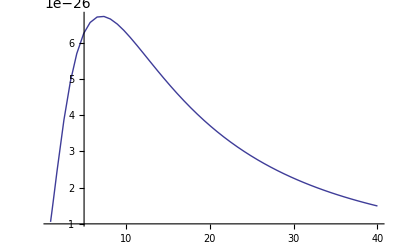

```mathematica
Plot[svnn[mpsi,114,10+mpsi,1000],{mpsi,1,40}]
```

InterpolatingFunction::dmval: Input value {620.378} lies outside the range of data in the interpolating function. Extrapolation will be used.

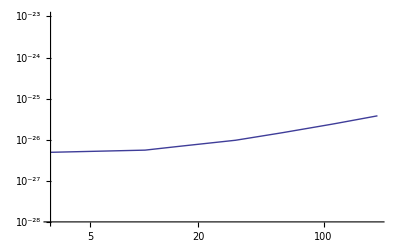

```mathematica
Get["/home/vanniagm/Dropbox/micromegas_3.6.9.2/DMSF2/fermilat.m"]
```

```mathematica
svbb[mpsi_,mudm3_,Lx_,Lam_,mphi_,z3_]:=(.001)^2*gevI2cm2(-3 (MB^2 (MB-mpsi) (MB+mpsi)Sqrt[1-MB^2/mpsi^2] (z3^2*mudm3^2+Lx vev^2 z3^2 Log[Lam/mphi])^2))/(256 ((GH^2 MH^2+(MH^2-4 mpsi^2)^2) Pi π^4 vev^4 Lam^2))
```

```mathematica
omnd=Join[ptsAbLuxND,ptsAbLuxND2];
omnd[[1]]
```

{2.5,1685.,193.9,193.9,-0.6,1.,0.12698,2.7531×10^-45,1.8438×10^-46,6.3725×10^-46,1.3421×10^8,0.0004778,0.12806,2.4014,0.0075156,0.1951}

```mathematica
omd=Join[ptsAbLuxD,ptsAbLuxD2];
```

```mathematica
omd[[1]]
```

{2.,1091.,36.36,36.36,0.,0.1683,0.1276,3.7836×10^-47,6.9231×10^-50,1.23×10^-47,24108.,3.9411×10^-8,0.000015981,2.4094,0.0060499,0.00005106}

```mathematica
Listsvnn=Table[{omnd[[i,1]],svnn[omnd[[i,1]],omnd[[i,3]],(10+omnd[[i,1]])*omnd[[i,6]],omnd[[i,2]]]},{i,1,Length[omnd]}];
Listsvnn2=Table[{omd[[i,1]],svnn[omd[[i,1]],omd[[i,3]],(10+omd[[i,1]])*omd[[i,6]],omd[[i,2]]]},{i,1,Length[omd]}];
```

```mathematica
Listsvff=Table[If[omnd[[i,1]]>MB,{omnd[[i,1]],svffZ[omnd[[i,1]],omnd[[i,2]],omnd[[i,4]],(10+omnd[[i,1]])*omnd[[i,6]],2,MB,gLmRb,3]},Unevaluated[Sequence[]]],{i,1,Length[omnd]}];
Listsvff2=Table[If[omd[[i,1]]>MB,{omd[[i,1]],svffZ[omd[[i,1]],omd[[i,2]],omd[[i,4]],(10+omd[[i,1]])*omd[[i,6]],2,MB,gLmRb,3]},Unevaluated[Sequence[]]],{i,1,Length[omd]}];
```

Check this results because sigmav was zero at first approx, it is missing a beta^2 factor, so it is expected to be lower.

```mathematica
Listsvbb=Table[{om[[i,1]],svbb[om[[i,1]],om[[i,4]],om[[i,5]],om[[i,2]],(10+om[[i,1]])*om[[i,6]],2]},{i,1,Length[om]}];
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvff[[All,{1,2}]],First];
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvff[[All,{1,2}]],First];
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->1];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->1];
```

{{5.,1.03905×10^-34},{5.5,2.60088×10^-34},{6.,3.36301×10^-34},{6.5,5.17779×10^-34},{7.,7.14264×10^-34},{7.5,1.00041×10^-33},{8.,1.3466×10^-33},{8.5,9.53585×10^-34},{9.,2.57352×10^-33},{9.5,2.8214×10^-33},{10.,3.14041×10^-33},{10.5,3.49817×10^-33},{11.,3.99477×10^-33},{11.5,4.59107×10^-33},{12.,6.26743×10^-33},{12.5,6.04106×10^-33},{13.,6.56952×10^-33},{13.5,9.61448×10^-33},{14.,1.04161×10^-32},{14.5,1.31459×10^-32},{15.,1.41976×10^-32},{15.5,1.23972×10^-32},{16.,1.33185×10^-32},{16.5,1.80551×10^-32},{17.,2.78535×10^-32},{17.5,2.92388×10^-32},{18.,3.07965×10^-32},{18.5,3.29955×10^-32},{19.,3.53309×10^-32},{19.5,4.6076×10^-32},{20.,4.0881×10^-32},{20.5,4.36723×10^-32},{21.,4.66477×10^-32},{21.5,7.48464×10^-32},{22.,8.00551×10^-32},{22.5,8.56319×10^-32},{23.,1.05625×10^-31},{23.5,1.13034×10^-31},{24.,1.21001×10^-31},{24.5,1.45574×10^-31},{25.,1.39703×10^-31},{25.5,1.49631×10^-31},{26.,1.60371×10^-31},{26.5,2.0263×10^-31},{27.,2.17564×10^-31},{27.5,2.33801×10^-31},{28.,2.51516×10^-31},{28.5,3.06978×10^-31},{29.,3.31087×10^-31},{30.,4.95791×10^-31},{30.5,5.37341×10^-31},{31.,5.83393×10^-31},{31.5,6.34656×10^-31},{55.5,3.12169×10^-31},{56.,6.71843×10^-32},{56.5,6.12438×10^-32},{57.,2.06186×10^-31},{57.5,2.34545×10^-33},{58.,0.},{58.5,0.},{59.,0.},{59.5,0.},{60.,0.},{60.5,0.},{61.,0.},{61.5,0.},{62.,0.},{62.5,1.10768×10^-31},{63.,3.74833×10^-31},{64.,1.79718×10^-31},{65.,1.62394×10^-31},{66.,1.47478×10^-31},{67.,1.34548×10^-31},{68.,1.23255×10^-31},{69.,1.13332×10^-31},{70.,1.53401×10^-31},{71.,1.42124×10^-31},{72.,1.32056×10^-31},{73.,1.23026×10^-31},{74.,1.14895×10^-31},{75.,1.07552×10^-31},{76.,1.30785×10^-31},{77.,1.23013×10^-31},{78.,1.15916×10^-31},{79.,1.09417×10^-31},{80.,1.03451×10^-31},{81.,1.37914×10^-34},{82.,1.12346×10^-31},{82.5,4.8537×10^-34},{83.,1.06733×10^-31},{84.,8.38843×10^-32},{85.,1.03114×10^-33},{86.,9.22127×10^-32},{87.,8.8026×10^-32},{88.,8.41211×10^-32},{89.,8.04643×10^-32},{90.,7.7043×10^-32},{92.,3.46964×10^-33},{92.5,2.23786×10^-34},{93.,2.18634×10^-34},{95.,6.27948×10^-32},{100.,2.51616×10^-36},{105.,4.39159×10^-32},{110.,3.74656×10^-32},{115.,3.2299×10^-32},{120.,2.80979×10^-32},{125.,1.90159×10^-33},{126.,6.00167×10^-34},{127.,8.79459×10^-35},{130.,4.54331×10^-37},{135.,1.93148×10^-32},{140.,3.25022×10^-33},{145.,2.89883×10^-33},{150.,1.39431×10^-32},{155.,1.15065×10^-34},{165.,3.39649×10^-33},{170.,3.09503×10^-33},{175.,2.82802×10^-33},{180.,9.58545×10^-33},{185.,2.59268×10^-34},{190.,8.17221×10^-33},{195.,3.03685×10^-33},{200.,2.81283×10^-33}}

{{5.,2.1999×10^-34},{5.5,4.21936×10^-34},{6.,6.37798×10^-34},{6.5,8.97111×10^-34},{7.,1.21614×10^-33},{7.5,1.58559×10^-33},{8.,2.05013×10^-33},{8.5,2.52232×10^-33},{9.,3.19456×10^-33},{9.5,4.00683×10^-33},{10.,4.85017×10^-33},{10.5,5.93193×10^-33},{11.,7.06779×10^-33},{11.5,8.53672×10^-33},{12.,1.00103×10^-32},{12.5,1.17111×10^-32},{13.,1.33048×10^-32},{13.5,1.51053×10^-32},{14.,1.70496×10^-32},{14.5,1.93605×10^-32},{15.,2.20841×10^-32},{15.5,2.50537×10^-32},{16.,2.77718×10^-32},{16.5,3.12637×10^-32},{17.,3.36303×10^-32},{17.5,3.78187×10^-32},{18.,4.32819×10^-32},{18.5,4.68388×10^-32},{19.,5.37303×10^-32},{19.5,5.87328×10^-32},{20.,6.45692×10^-32},{20.5,6.91468×10^-32},{21.,7.97033×10^-32},{21.5,8.94857×10^-32},{22.,9.57902×10^-32},{22.5,1.10206×10^-31},{23.,1.17997×10^-31},{23.5,1.3612×10^-31},{24.,1.45793×10^-31},{24.5,1.67268×10^-31},{25.,1.79309×10^-31},{25.5,1.9232×10^-31},{26.,2.14474×10^-31},{26.5,2.4784×10^-31},{27.,2.6635×10^-31},{27.5,2.86492×10^-31},{28.,3.0848×10^-31},{28.5,3.06978×10^-31},{29.,3.31087×10^-31},{30.,4.95791×10^-31},{30.5,5.37341×10^-31},{31.,5.83393×10^-31},{31.5,6.34656×10^-31},{55.5,1.81691×10^-30},{56.,2.10082×10^-30},{56.5,1.92317×10^-30},{57.,1.76767×10^-30},{57.5,1.28372×10^-30},{58.,1.30648×10^-30},{58.5,1.21346×10^-30},{59.,1.0228×10^-30},{59.5,9.55402×10^-31},{60.,8.29979×10^-31},{60.5,7.7911×10^-31},{61.,7.31917×10^-31},{61.5,6.89687×10^-31},{62.,6.51123×10^-31},{62.5,8.84358×10^-31},{63.,1.22265×10^-30},{64.,1.10388×10^-30},{65.,1.00227×10^-30},{66.,9.14601×10^-31},{67.,8.3841×10^-31},{68.,7.71724×10^-31},{69.,7.12996×10^-31},{70.,6.36101×10^-31},{71.,5.91383×10^-31},{72.,5.5139×10^-31},{73.,5.15467×10^-31},{74.,4.83068×10^-31},{75.,4.53752×10^-31},{76.,4.27118×10^-31},{77.,4.02855×10^-31},{78.,3.80672×10^-31},{79.,3.60333×10^-31},{80.,3.41635×10^-31},{81.,2.99384×10^-31},{82.,2.54855×10^-31},{82.5,9.503×10^-33},{83.,2.21358×10^-31},{84.,1.95488×10^-31},{85.,1.78307×10^-31},{86.,1.61856×10^-31},{87.,1.45568×10^-31},{88.,1.30207×10^-31},{89.,1.24671×10^-31},{90.,1.10422×10^-31},{92.,1.16362×10^-31},{92.5,6.25406×10^-33},{93.,1.1343×10^-31},{95.,8.20164×10^-32},{100.,9.87092×10^-32},{105.,5.11376×10^-32},{110.,3.74656×10^-32},{115.,3.2299×10^-32},{120.,2.80979×10^-32},{125.,2.46347×10^-32},{126.,4.4765×10^-32},{127.,2.2208×10^-33},{130.,4.0085×10^-32},{135.,1.93148×10^-32},{140.,1.72456×10^-32},{145.,1.54738×10^-32},{150.,1.39431×10^-32},{155.,2.29414×10^-32},{165.,1.24008×10^-32},{170.,1.13499×10^-32},{175.,1.0417×10^-32},{180.,9.58545×10^-33},{185.,8.8408×10^-33},{190.,8.17221×10^-33},{195.,7.56995×10^-33},{200.,2.81283×10^-33}}

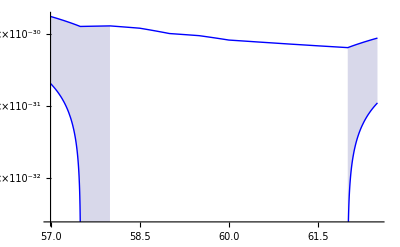

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvff2[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvff2[[All,{1,2}]],First]
fis2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fis22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

InterpolatingFunction::dmval: Input value {2.00059} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {686.725} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

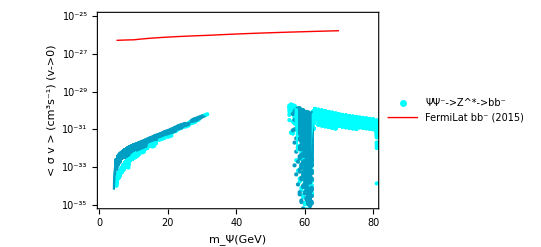

```mathematica
fsvbb=Show[ListLogPlot[{Listsvff2,Listsvff},PlotRange->{{1,80},{10^-35,10^-25}},PlotStyle->{Cyan,RGBColor[0,0.62,0.76]},PlotLegends->Placed[PointLegend[{"ΨΨ^-->Z^*->bb^-"(*,"ΨΨ^-->H^*->bb^-"*)},LabelStyle->16,LegendFunction->"Frame",Background->White],{0.65,.49}]],
LogPlot[{Fb1[m],Fb2[m]},{m,2,31},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],LogPlot[{fis2[m],fis22[m]},{m,57,80},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->Cyan],
LogPlot[Subscript[Φ,μ][m],{m,5,70},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{Red},{"FermiLat \!\(\*SuperscriptBox[\(bb\), \(-\)]\) (2015)"},LabelStyle->16],{0.65,.87}]],Frame->True,
FrameLabel->{"m_Ψ(GeV)","< σ v > (\!\(\*SuperscriptBox[\(cm\), \(3\)]\)\!\(\*SuperscriptBox[\(s\), \(-1\)]\)) (v->0)"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["FermilatLux.pdf",fsvbb]
```

FermilatLux.pdf

InterpolatingFunction::dmval: Input value {464.989} lies outside the range of data in the interpolating function. Extrapolation will be used.

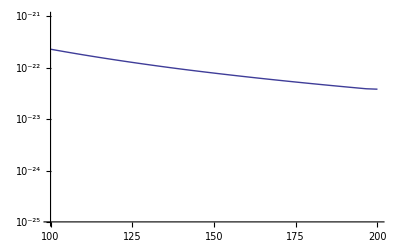

```mathematica
Get["/home/vanniagm/Dropbox/nu_portal/MATH_NUMODEL/icecube.m"]
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvnn[[All,{1,2}]],First];
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvnn[[All,{1,2}]],First];
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->2];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->2];
```

{{57.,6.36384×10^-27},{58.,6.50272×10^-28},{59.,4.97209×10^-29},{60.,4.6143×10^-30},{61.,8.92461×10^-31},{62.,1.21329×10^-30}}

{{57.,7.38017×10^-27},{58.,2.40917×10^-27},{59.,4.39714×10^-27},{60.,8.9742×10^-27},{61.,1.66732×10^-27},{62.,9.3953×10^-28}}

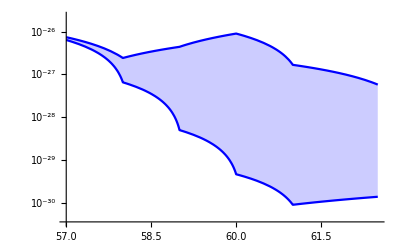

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvnn2[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvnn2[[All,{1,2}]],First]
fis2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fis22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

InterpolatingFunction::dmval: Input value {464.989} lies outside the range of data in the interpolating function. Extrapolation will be used.

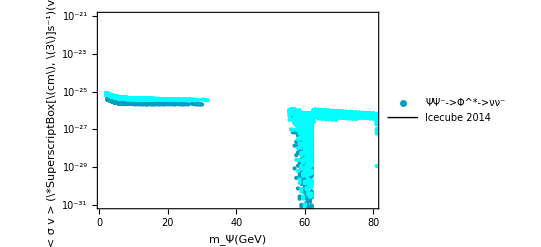

```mathematica
fsvnn=Show[ListLogPlot[{Listsvnn,Listsvnn2},PlotRange->{{1,80},{10^-31,10^-21}},PlotStyle->{RGBColor[0,0.62,0.76],Cyan},PlotLegends->Placed[PointLegend[{"ΨΨ^-->Φ^*->νν^-"},LabelStyle->16,LegendFunction->"Frame",Background->White],{0.65,.2}]],LogPlot[Subscript[Φ,μ][m],{m,100,200},PlotStyle->{Black},PlotRange->{10^-31,10^-21},PlotLegends->Placed[LineLegend[{Black},{"Icecube 2014"},LabelStyle->16],{0.68,.82}]],(*LogPlot[{Fb1[m],Fb2[m]},{m,4,35},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],LogPlot[{fis2[m],fis22[m]},{m,57,63},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]],*)Frame->True,FrameLabel->{"m_Ψ(GeV)","< σ v > (\*SuperscriptBox[\(cm\), \(3\)]s^-1)(v->0)"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["SVnunuLux.pdf",fsvnn]
```

SVnunuLux.pdf

Neutrino Flux

```mathematica
km2yeartocm2s=1/(365*24*3600*10^10);
km3yeartocm3s=1/(365*24*3600*10^15);
```

```mathematica
listFluxnuCon=Table[{omnd[[i,1]],omnd[[i,13]]*km3yeartocm3s},{i,1,Length[omnd]}];
listFluxnuCon2=Table[{omd[[i,1]],omd[[i,13]]*km3yeartocm3s},{i,1,Length[omd]}];
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCon[[All,{1,2}]],First];
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCon[[All,{1,2}]],First];
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->2];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->2];
```

{{57.,1.07135×10^-23},{58.,1.48288×10^-25},{59.,2.82528×10^-27},{60.,1.6042×10^-28},{61.,3.79059×10^-29},{62.,3.44527×10^-29}}

{{57.,1.81019×10^-23},{58.,8.58416×10^-24},{59.,6.95269×10^-23},{60.,1.57953×10^-22},{61.,2.16759×10^-24},{62.,1.2916×10^-24}}

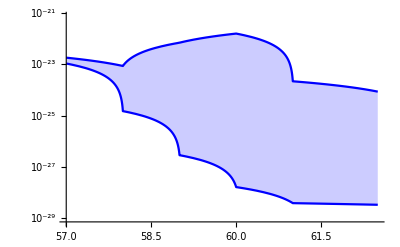

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCon2[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCon2[[All,{1,2}]],First]
fis2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fis22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

```mathematica
listFluxnuUp=Table[{omnd[[i,1]],omnd[[i,12]]*km2yeartocm2s},{i,1,Length[omnd]}];
listFluxnuUp2=Table[{omd[[i,1]],omd[[i,12]]*km2yeartocm2s},{i,1,Length[omd]}];
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUp[[All,{1,2}]],First];
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUp[[All,{1,2}]],First];
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->2];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->2];
```

{{57.,1.1061×10^-19},{58.,1.55296×10^-21},{59.,2.9921×10^-23},{60.,1.71455×10^-24},{61.,4.11847×10^-25},{62.,3.7963×10^-25}}

{{57.,1.86891×10^-19},{58.,8.98656×10^-20},{59.,7.38838×10^-19},{60.,1.7025×10^-18},{61.,2.36863×10^-20},{62.,1.42704×10^-20}}

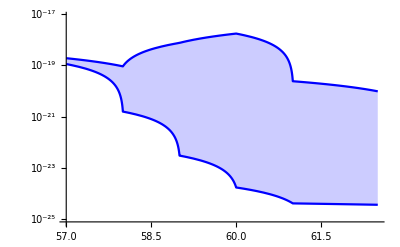

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUp2[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUp2[[All,{1,2}]],First]
fis2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fis22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

```mathematica
Max[Table[om[[i,13]]*km2yeartocm2s,{i,1,Length[om]}]]
```

1.85325×10^-17

```mathematica
graphflux1=Show[ListLogPlot[{listFluxnuCon,listFluxnuCon2},PlotRange->{{1,80},{10^-25,10^-17}},PlotStyle->{RGBColor[0,0.62,0.76],Cyan}],
(*LogPlot[{Fb1[m],Fb2[m]},{m,4,35},PlotStyle->{RGBColor[0,0.62,0.76],RGBCo0lor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],
LogPlot[{fis2[m],fis22[m]},{m,57,63},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]],*)Frame->True,FrameLabel->{"m_Ψ(GeV)","WIMP-induced \n muon  contained flux (\!\(\*SuperscriptBox[\(cm\), \(-3\)]\)\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

-Graphics-

```mathematica
graphflux2=Show[ListLogPlot[{listFluxnuUp,listFluxnuUp2},PlotRange->{{1,80},{10^-25,10^-16}},PlotStyle->{RGBColor[0,0.62,0.76],Cyan}],
(*LogPlot[{Fb1[m],Fb2[m]},{m,4,35},PlotStyle->{RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],
LogPlot[{fis2[m],fis22[m]},{m,57,63},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]],*)Frame->True,FrameLabel->{"m_Ψ(GeV)","WIMP-induced \n up-muon flux (\!\(\*SuperscriptBox[\(cm\), \(-2\)]\)\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

-Graphics-

```mathematica
Export["UpMuonLux.pdf",graphflux2]
```

UpMuonLux.pdf

UpMuon.pdf

```mathematica
Export["MuonContLux.pdf",graphflux1]
```

MuonContLux.pdf

MuonCont.pdf

```mathematica
ParentDirectory[]
```

/home/vanniagm/Dropbox/micromegas_3.6.9.2

```mathematica
graphflux1=Show[ListLogPlot[Table[{om[[i,1]],om[[i,13]]*km2yeartocm2s},{i,1,Length[om]}],PlotRange->{10^-38,10^-14},Frame->{True,True,False,False},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ψ\)]\)(GeV)","WIMP-induced \n up-muon flux (\!\(\*SuperscriptBox[\(cm\), \(-2\)]\)\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},LabelStyle->{FontWeight->"Bold",FontSize->18}],ImageSize->{GoldenRatio*500,500}]
```

-Graphics-

Conversions

Ciii=Sqrt[2]*z3*mudm1/vev;
Cii=2*((Lam^2/vev^2)z3^2mudm3^2/Lam^2+Lx+z3^2*Log[Lam/mphi]);
CViiL=(Lam^2/vev^2)(z3^2 mudm3^2/Lam^2);
CViiR=(Lam^2/vev^2)(z3^2 mudm3^2/Lam^2)(Log[Lam/mphi]);

Higgs decay exluded region

```mathematica
om[[100]]
```

{4.,1000.,100.,13.1,0.3,1.,0.11304,1.1634×10^-46,9.6744×10^-47,1.0805×10^-46,1.7177×10^6,0.000023146,0.0030811,2.4068,0.0073165,0.1732}

```mathematica
Max[Table[(10+om[[i,1]])*om[[i,6]],{i,1,Length[om]}]]
```

288.

```mathematica
Max[Table[om[[i,6]],{i,1,Length[om]}]]
```

4.

```mathematica
vev=246;
```

```mathematica
RegHinv[Lam_,zz_,mu1_,mu3_,Lx_,ms_]:=(vev/Lam)Abs[(zz^2)((mu1^2+mu3^2)/vev^2+Lx*Log[Lam/ms])];
```

```mathematica
plot1=RegionPlot[RegHinv[1000,2,118,118,lx,ms]<1.3,{lx,-1,1},{ms,10,288},Frame->True,FrameLabel->{"λ_x","m_Φ",None,None}]
```

-Graphics-

```mathematica
Export["plot1.pdf",plot1]
```

plot1.pdf

```mathematica
vev=246;
```

```mathematica
RegHinv[Lam_,zz_,mu1_,mu3_,Lx_,ms_]:=(vev/Lam)Abs[(zz^2)((mu1^2+mu3^2)/vev^2+Lx*Log[Lam/ms])];
```

```mathematica
RegionPlot[RegHinv[Lam,2,118,118,lx,288]<1.3,{lx,-1,1},{Lam,1000,10000}]
```

-Graphics-

```mathematica
RegionPlot[RegHinv[1000,2,mu,118,lx,288]<1.3,{lx,-1,1},{mu,1,118}]
```

-Graphics-

```mathematica
Sqrt[.0022/(125/(512*Pi^5))]
```

1.6606